# Direct Hubble Measurements with EEM (SN within Hubble Flow)

### Setup/Imports

```mathematica
ClearAll["Global`*"]
```

```mathematica
<<MaTeX`
```

```mathematica
linTick[iTick_,fTick_,magnification_:2,interval_:1]:=(LocalTick[j_]:=Table[{j+Log10[k],""},{k,2,9}];
LocalTickLinear[j_]:=Table[{j+k,""},{k,interval*0.1,interval*0.9,interval*.1}];
linearTab=Flatten[Table[Join[{{i,MaTeX[ToString[NumberForm[i,{∞,1}]],Magnification->magnification],{0.025,0}}},LocalTickLinear[i]],{i,iTick,fTick,interval}],1])

logTick[iTick_,fTick_,magnification_:2,interval_:1]:=(LocalTick[j_]:=Table[{j+Log10[k],""},{k,2,9}];
logTab=Flatten[Table[Join[{{i,Which[!IntegerQ[i/interval],MaTeX["",Magnification->magnification],i==0,MaTeX[1,Magnification->magnification],i==1,MaTeX[10,Magnification->magnification],True,MaTeX[Power[10,ToString[i]],Magnification->magnification]],{0.025,0}}},LocalTick[i]],{i,iTick,fTick}],1])

linTickNone[iTick_,fTick_,magnification_:2,interval_:1]:=(LocalTick[j_]:=Table[{j+Log10[k],""},{k,2,9}];
LocalTickLinear[j_]:=Table[{j+k,""},{k,interval*0.1,interval*0.9,interval*.1}];
linearTab=Flatten[Table[Join[{{i,"",{0.025,0}}},LocalTickLinear[i]],{i,iTick,fTick,interval}],1])

logTickNone[iTick_,fTick_,magnification_:2,interval_:1]:=(LocalTick[j_]:=Table[{j+Log10[k],""},{k,2,9}];
logTab=Flatten[Table[Join[{{i,"",{0.025,0}}},LocalTick[i]],{i,iTick,fTick}],1])

linTick2[iTick_,fTick_,magnification_:2,interval_:1, interval2_:1]:=(LocalTick[j_]:=Table[{j+Log10[k],""},{k,2,9}];
LocalTickLinear[j_]:=Table[{j+k,""},{k,interval2*0.1,interval2*0.9,interval2*.1}];
linearTab=Flatten[Table[Join[{{i,MaTeX[ToString[NumberForm[i,{∞,1}]],Magnification->magnification],{0.025,0}}},LocalTickLinear[i]],{i,iTick,fTick,interval}],1])

linTick3[iTick_,fTick_,magnification_:2,interval_:1, interval2_:1]:=(LocalTick[j_]:=Table[{j+Log10[k],""},{k,2,9}];
LocalTickLinear[j_]:=Table[{j+k,""},{k,interval2*0.1,interval2*0.9,interval2*.1}];
linearTab=Flatten[Table[Join[{{i,MaTeX[ToString[NumberForm[i,{∞,2}]],Magnification->magnification],{0.025,0}}},LocalTickLinear[i]],{i,iTick,fTick,interval}],1])
```

```mathematica
color[i_]:=ColorData[97,"ColorList"][[i]];
changeStyle[col_][Graphics[items_,opt___]]:=Graphics[{col,items},opt]
```

```mathematica
(*Find roots more accurately than Mathematica's FindRoot. Used later to find axion decay temperature*)
Clear[findAllRoots]
SyntaxInformation[findAllRoots]={"LocalVariables"->{"Plot",{2,2}},"ArgumentsPattern"->{_,_,OptionsPattern[]}};
SetAttributes[findAllRoots,HoldAll];

Options[findAllRoots]=Join[{"ShowPlot"->False,PlotRange->All},FilterRules[Options[Plot],Except[PlotRange]]];

findAllRoots[fn_,{l_,lmin_,lmax_},opts:OptionsPattern[]]:=Module[{pl,p,x,localFunction,brackets},localFunction=ReleaseHold[Hold[fn]/.HoldPattern[l]:>x];
If[lmin≠lmax,pl=Plot[localFunction,{x,lmin,lmax},Evaluate@FilterRules[Join[{opts},Options[findAllRoots]],Options[Plot]]];
p=Cases[pl,Line[{x__}]:>x,Infinity];
If[OptionValue["ShowPlot"],Print[Show[pl,PlotLabel->"Finding roots for this function",ImageSize->200,BaseStyle->{FontSize->8}]]],p={}];
brackets=Map[First,Select[(*This Split trick pretends that two points on the curve are "equal" if the function values have _opposite _ sign.Pairs of such sign-changes form the brackets for the subsequent FindRoot*)Split[p,Sign[Last[#2]]==-Sign[Last[#1]]&],Length[#1]==2&],{2}];
x/.Apply[FindRoot[localFunction==0,{x,##1}]&,brackets,{1}]/.x->{}];
```

```mathematica
trimPoint=Sequence[NumberFormat->(DisplayForm@RowBox[Join[{StringTrim[#1,RegularExpression["\\.$"]]},If[#3≠"",{"×",SuperscriptBox[#2,#3]},{}]]]&)]//Quiet;

toScientificNotation[x_?NumericQ,digits_:2]:=Which[Denominator[x]===1,
ScientificForm[x,digits],True,ScientificForm[N[x,digits],trimPoint]]

toTeX[x_?NumericQ,digits_:2]:=ToString[TeXForm[toScientificNotation[x]]]//Quiet
```

### Colorblind Colors

```mathematica
xgfsnormal6Tab={{64,83,211},{221,179,16},{181,29,20},{0,190,255},{251,73,176},{0,178,93},{202,202,202}};
xgfsnormal12Tab={{235,172,35},{184,0,88},{0,140,249},{0,110,0},{0,187,173},{209,99,230},{178,69,2},{255,146,135},{89,84,214},{0,198,248},{135,133,0},{0,167,108},{189,189,189}};
xgfsbright6Tab={{239,230,69},{233,53,161},{0,227,255},{225,86,44},{83,126,255},{0,203,133},{238,238,238}};
xgfsdark6Tab={{0,89,0},{0,0,120},{73,13,0},{138,3,79},{0,90,138},{68,53,0},{88,88,88}};
xgfsfancy6Tab={{86,100,26},{192,175,251},{230,161,118},{0,103,138},{152,68,100},{94,204,171},{205,205,205}};
xgfstarnish6Tab={{39,77,82},{199,162,166},{129,139,112},{96,78,60},{140,159,183},{121,104,128},{192,192,192}};
```

```mathematica
xgfsnormal6TabColors=Table[RGBColor[xgfsnormal6Tab[[i]]/256],{i,1,Length[xgfsnormal6Tab]}]
xgfsnormal12TabColors=Table[RGBColor[xgfsnormal12Tab[[i]]/256],{i,1,Length[xgfsnormal12Tab]}]
xgfsbright6TabColors=Table[RGBColor[xgfsbright6Tab[[i]]/256],{i,1,Length[xgfsbright6Tab]}]
xgfsdark6TabColors=Table[RGBColor[xgfsdark6Tab[[i]]/256],{i,1,Length[xgfsdark6Tab]}]
xgfsfancy6TabColors=Table[RGBColor[xgfsfancy6Tab[[i]]/256],{i,1,Length[xgfsfancy6Tab]}]
xgfstarnish6TabColors=Table[RGBColor[xgfstarnish6Tab[[i]]/256],{i,1,Length[xgfstarnish6Tab]}]
```

{RGBColor[{Rational[1, 4], Rational[83, 256], Rational[211, 256]}],RGBColor[{Rational[221, 256], Rational[179, 256], Rational[1, 16]}],RGBColor[{Rational[181, 256], Rational[29, 256], Rational[5, 64]}],RGBColor[{0, Rational[95, 128], Rational[255, 256]}],RGBColor[{Rational[251, 256], Rational[73, 256], Rational[11, 16]}],RGBColor[{0, Rational[89, 128], Rational[93, 256]}],RGBColor[{Rational[101, 128], Rational[101, 128], Rational[101, 128]}]}

{RGBColor[{Rational[235, 256], Rational[43, 64], Rational[35, 256]}],RGBColor[{Rational[23, 32], 0, Rational[11, 32]}],RGBColor[{0, Rational[35, 64], Rational[249, 256]}],RGBColor[{0, Rational[55, 128], 0}],RGBColor[{0, Rational[187, 256], Rational[173, 256]}],RGBColor[{Rational[209, 256], Rational[99, 256], Rational[115, 128]}],RGBColor[{Rational[89, 128], Rational[69, 256], Rational[1, 128]}],RGBColor[{Rational[255, 256], Rational[73, 128], Rational[135, 256]}],RGBColor[{Rational[89, 256], Rational[21, 64], Rational[107, 128]}],RGBColor[{0, Rational[99, 128], Rational[31, 32]}],RGBColor[{Rational[135, 256], Rational[133, 256], 0}],RGBColor[{0, Rational[167, 256], Rational[27, 64]}],RGBColor[{Rational[189, 256], Rational[189, 256], Rational[189, 256]}]}

{RGBColor[{Rational[239, 256], Rational[115, 128], Rational[69, 256]}],RGBColor[{Rational[233, 256], Rational[53, 256], Rational[161, 256]}],RGBColor[{0, Rational[227, 256], Rational[255, 256]}],RGBColor[{Rational[225, 256], Rational[43, 128], Rational[11, 64]}],RGBColor[{Rational[83, 256], Rational[63, 128], Rational[255, 256]}],RGBColor[{0, Rational[203, 256], Rational[133, 256]}],RGBColor[{Rational[119, 128], Rational[119, 128], Rational[119, 128]}]}

{RGBColor[{0, Rational[89, 256], 0}],RGBColor[{0, 0, Rational[15, 32]}],RGBColor[{Rational[73, 256], Rational[13, 256], 0}],RGBColor[{Rational[69, 128], Rational[3, 256], Rational[79, 256]}],RGBColor[{0, Rational[45, 128], Rational[69, 128]}],RGBColor[{Rational[17, 64], Rational[53, 256], 0}],RGBColor[{Rational[11, 32], Rational[11, 32], Rational[11, 32]}]}

{RGBColor[{Rational[43, 128], Rational[25, 64], Rational[13, 128]}],RGBColor[{Rational[3, 4], Rational[175, 256], Rational[251, 256]}],RGBColor[{Rational[115, 128], Rational[161, 256], Rational[59, 128]}],RGBColor[{0, Rational[103, 256], Rational[69, 128]}],RGBColor[{Rational[19, 32], Rational[17, 64], Rational[25, 64]}],RGBColor[{Rational[47, 128], Rational[51, 64], Rational[171, 256]}],RGBColor[{Rational[205, 256], Rational[205, 256], Rational[205, 256]}]}

{RGBColor[{Rational[39, 256], Rational[77, 256], Rational[41, 128]}],RGBColor[{Rational[199, 256], Rational[81, 128], Rational[83, 128]}],RGBColor[{Rational[129, 256], Rational[139, 256], Rational[7, 16]}],RGBColor[{Rational[3, 8], Rational[39, 128], Rational[15, 64]}],RGBColor[{Rational[35, 64], Rational[159, 256], Rational[183, 256]}],RGBColor[{Rational[121, 256], Rational[13, 32], Rational[1, 2]}],RGBColor[{Rational[3, 4], Rational[3, 4], Rational[3, 4]}]}

## Individual σ_H0/H0 (stat)

##### Parameters

```mathematica
H0=70; (*70 km/s per Mpc*)
t0=6; (*6 hr observation time*)
(*σDOverD0StageII=10^-1;*)(*Standard devation in distance measurment in Mpc for observing a standard SN for 6 hr at 10 Mpc*)
σv0=250;(*Standard devation in redshift velocity measurment in km/s for observing a SN*)
D0=1; (*1 Mpc for normalization*)
MSNII=-16.1;(*Type II absolute magnitude. From Nearby Supernova Rates from the Lick Observatory Supernova Search by Fillipenko and others*)
MSNIa=-18.5;(*Type Ia absolute magnitude. From Nearby Supernova Rates from the Lick Observatory Supernova Search by Fillipenko and others*)
```

σH^2=((∂H)/(∂v))^2 σv^2+((∂H)/(∂D))^2 σD^2, H = v/D
=(1/D)^2 σv^2+(v/D^2)^2 σD^2

so that

σH^2/H^2=D^2/v^2((1/D)^2 σv^2+(v/D^2)^2 σD^2)=σv^2/v^2+σD^2/D^2

According to Calvin's sims,

σD/D=0.1*10^(0.4(m-12.5))(t/(6hr))^(-1/2)*(σt/(10ps))^(1/2)(A/(π*(5m)^2))^-1*(R/10^4)^(-1/2)(nArr/1)^-1
≡(σD/D)_0 10^(0.4(m-12.5))*(t/t0)^(-1/2),

with t0=  6hr and(σD/D)_0=0.1*(σt/(10ps))^(1/2)(A/(π*(5m)^2))^-1*(R/10^4)^(-1/2)(nArr/1)^-1 , normalized for stage II parameters


D(m)=D0*10^((mag-MSNII-25)/5), D0=1Mpc


so 
σH^2/H^2=σv^2/(H0^2*D^2)+σD^2/D^2=σv^2/(H0^2*D0^2)10^(-2/5(mag-MSN-25))+((σD/D)^2)_0 10^(0.8(m-12.5))*(t/t0)^-1

```mathematica
σtIII=3; (*Subscript[σ, t] for phase III in ps*)
σtII=10; (*Subscript[σ, t] for phase II in ps*)
RIII=2*10^4; (*Spectral resolution for phase III*)
RII=1*10^4;(*Spectral resolution for phase II*)
nIII=10;(*Number pair arrays for phase III*)
nII=1;(*Number pair arrays for phase II*)

telescopeRadiusII=5;(*Telescope radius in meters of phase II*)
telescopeRadiusIII=5;(*Telescope radius in meters of phase III*)

efficiencyFactor=1/2;

figureOfMerit[σtps_,Rspectral_,nArr_,telescopeRadius_,efficiency_]:=σtps^(-1/2)Rspectral^(1/2)nArr*(π*telescopeRadius^2)*efficiency
```

```mathematica
figureOfMeritStnd=figureOfMerit[σtII,RII,nII,telescopeRadiusII,efficiencyFactor]//N
```

1241.82

```mathematica
matchLightLow=500;
```

```mathematica
matchLightStnd=figureOfMeritStnd
```

1241.82

```mathematica
matchLightMidRange=10*matchLightStnd
```

12418.2

```mathematica
matchLightSuper=matchLightMidRange/matchLightLow*matchLightMidRange
```

308425.

```mathematica
lowMatchlightPaper=1250;
highMatchlightPaper=5*10^4;
```

```mathematica
2*(60/6)^(1/2)//N
```

6.32456

```mathematica
σDoverDEEM[matchlight_,m_,tObshour_]:=6.3*10^-2*10^(0.4*(m-12))*(tObshour/6)^(-1/2)(matchlight/matchLightStnd)^-1
```

```mathematica
6.3/(10*10^(-0.4*0.5))
```

0.998483

```mathematica
Dofm[m_,MSN_]:=D0*10^((m-MSN-25)/5)

σH0OverH0[σv0_,m_,MSN_,tObshour_,matchlight_]:=
√(σv0^2/(H0^2*Dofm[m,MSN]^2)+σDoverDEEM[matchlight,m,tObshour]^2)
```

##### Distance Ticks for Type II and Type Ia

```mathematica
μ[D_]:=5*Log10[D]+25
```

```mathematica
magTypeII[D_]:=μ[D]+MSNII;
magTypeIa[D_]:=μ[D]+MSNIa;
```

```mathematica
typeIITick[j_]:=Table[{magTypeII[10^(j+Log10[k])],""},{k,2,10}]
typeIaTick[j_]:=Table[{magTypeIa[10^(j+Log10[k])],""},{k,2,10}]

dTabTypeII=Flatten[Table[Join[{{magTypeII[10^j],Which[(*EvenQ[j],"",*)j==0,MaTeX[1,Magnification->1.5],j==1,MaTeX[10,Magnification->1.5],True,MaTeX[Power[10,ToString[j]],Magnification->1.5]],{0.025,0}}},typeIITick[j]],{j,-1,4,1}],1];

dTabTypeIa=Flatten[Table[Join[{{magTypeIa[10^j],Which[(*EvenQ[j],"",*)j==0,MaTeX[1,Magnification->1.5],j==1,MaTeX[10,Magnification->1.5],True,MaTeX[Power[10,ToString[j]],Magnification->1.5]],{0.025,0}}},typeIaTick[j]],{j,-1,4,1}],1];
```

##### Individual Uncertainty Plots Type II

```mathematica
tObsTotal=30*6;
```

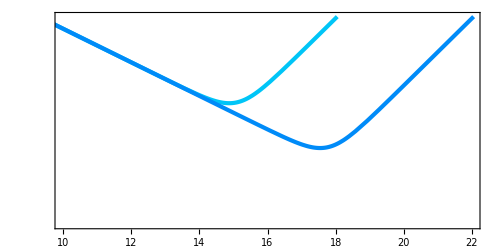

```mathematica
(*σHOverHPlotStageSNTypeII=Plot[{
Log10[σH0OverH0[σv0,mag,MSNII,tObsTotal,matchLightLow]],
Log10[σH0OverH0[σv0,mag,MSNII,tObsTotal,matchLightMidRange]],
Log10[σH0OverH0[σv0,mag,MSNII,tObsTotal,matchLightSuper]]
},{mag,7.5,25},
PlotStyle->{
{xgfsnormal12TabColors[[10]],AbsoluteThickness[3]},
{xgfsnormal12TabColors[[3]],AbsoluteThickness[3]},
{Lighter[xgfsdark6TabColors[[2]],.25],AbsoluteThickness[3]}
},
Frame->True,PlotRange->{{10,22},{-2.0,1.0}},Frame->True,Axes->False,
FrameTicks->{{logTick[-2,1,1.5,1],logTickNone[-2,1,1.5,1]},{linTick2[0,25,1.5,1,4],dTabTypeII}},
FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],FrameLabel->{{MaTeX["\\text{Individual SN }(\\sigma_{H}/H)_{\\rm stat}" ,Magnification->1.5],None},{MaTeX["m \\, [\\rm{ Mag]}",Magnification->1.5],None(*,MaTeX["\\text{SN Distance [Mpc]}",Magnification->1.5]*)}},ImageSize->500,ImagePadding->{{80,20},{70,30}},ImageSize->500,AspectRatio->1/2]*)
σHOverHPlotStageSNTypeII=Plot[{
Log10[σH0OverH0[σv0,mag,MSNII,tObsTotal,lowMatchlightPaper]],
Log10[σH0OverH0[σv0,mag,MSNII,tObsTotal,highMatchlightPaper]]
},{mag,7.5,25},
PlotStyle->{
{xgfsnormal12TabColors[[10]],AbsoluteThickness[3]},
{xgfsnormal12TabColors[[3]],AbsoluteThickness[3]},
{Lighter[xgfsdark6TabColors[[2]],.25],AbsoluteThickness[3]}
},
Frame->True,PlotRange->{{10,22},{Log10[1*10^-2],Log10[3]}},Frame->True,Axes->False,
FrameTicks->{{logTick[-2,1,1.5,1],logTickNone[-2,1,1.5,1]},{linTick2[0,25,1.5,1,4],dTabTypeII}},
FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],FrameLabel->{{MaTeX["\\text{Individual SN }(\\sigma_{H}/H)_{\\rm stat}" ,Magnification->1.5],None},{MaTeX["m \\, [\\rm{ Mag]}",Magnification->1.5],None(*,MaTeX["\\text{SN Distance [Mpc]}",Magnification->1.5]*)}},ImageSize->500,ImagePadding->{{80,20},{70,30}},ImageSize->500,AspectRatio->1/2]
```

##### Individual Uncertainty Plots Type Ia

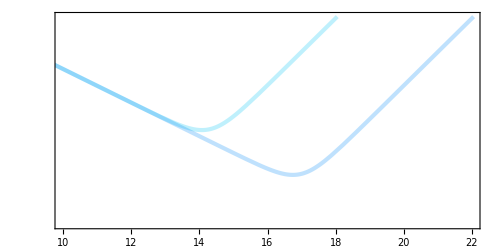

```mathematica
(*σHOverHPlotStageSNTypeIa=Plot[{
Log10[σH0OverH0[σv0,mag,MSNIa,tObsTotal,matchLightLow]],
Log10[σH0OverH0[σv0,mag,MSNIa,tObsTotal,matchLightMidRange]],
Log10[σH0OverH0[σv0,mag,MSNIa,tObsTotal,matchLightSuper]]
},{mag,7.5,25},
PlotStyle->{
(*{xgfsnormal12TabColors[[1]],AbsoluteThickness[3](*,Dashed*)},
{xgfsnormal12TabColors[[8]],AbsoluteThickness[3](*,Dashed*)},
{xgfsnormal12TabColors[[7]],AbsoluteThickness[3](*,Dashed*)}*)
{xgfsnormal12TabColors[[10]],AbsoluteThickness[3],Opacity[.25]},
{xgfsnormal12TabColors[[3]],AbsoluteThickness[3],Opacity[.25]},{Lighter[xgfsdark6TabColors[[2]],.25],AbsoluteThickness[3],Opacity[.25]}
},
Frame->True,PlotRange->{{10,22},{-2.0,1.0}},Frame->True,Axes->False,
FrameTicks->{{logTick[-2,1,1.5,1],logTickNone[-2,1,1.5,1]},{linTick2[0,25,1.5,1,4],dTabTypeIa}},
FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],FrameLabel->{{MaTeX["\\text{Individual SN }(\\sigma_{H}/H)_{\\rm stat}" ,Magnification->1.5],None},{MaTeX["m \\, [\\rm{ Mag]}",Magnification->1.5],None(*,MaTeX["\\text{SN Distance [Mpc]}",Magnification->1.5]*)}},ImageSize->500,ImagePadding->{{80,20},{70,30}},ImageSize->500,AspectRatio->1/2]*)
σHOverHPlotStageSNTypeIa=Plot[{
Log10[σH0OverH0[σv0,mag,MSNIa,tObsTotal,lowMatchlightPaper]],
Log10[σH0OverH0[σv0,mag,MSNIa,tObsTotal,highMatchlightPaper]]
},{mag,7.5,25},
PlotStyle->{
(*{xgfsnormal12TabColors[[1]],AbsoluteThickness[3](*,Dashed*)},
{xgfsnormal12TabColors[[8]],AbsoluteThickness[3](*,Dashed*)},
{xgfsnormal12TabColors[[7]],AbsoluteThickness[3](*,Dashed*)}*)
{xgfsnormal12TabColors[[10]],AbsoluteThickness[3],Opacity[.25]},
{xgfsnormal12TabColors[[3]],AbsoluteThickness[3],Opacity[.25]},{Lighter[xgfsdark6TabColors[[2]],.25],AbsoluteThickness[3],Opacity[.25]}
},
Frame->True,PlotRange->{{10,22},{Log10[1*10^-2],Log10[3]}},Frame->True,Axes->False,
FrameTicks->{{logTick[-2,1,1.5,1],logTickNone[-2,1,1.5,1]},{linTick2[0,25,1.5,1,4],dTabTypeIa}},
FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],FrameLabel->{{MaTeX["\\text{Individual SN }(\\sigma_{H}/H)_{\\rm stat}" ,Magnification->1.5],None},{MaTeX["m \\, [\\rm{ Mag]}",Magnification->1.5],None(*,MaTeX["\\text{SN Distance [Mpc]}",Magnification->1.5]*)}},ImageSize->500,ImagePadding->{{80,20},{70,30}},ImageSize->500,AspectRatio->1/2]
```

```mathematica
centerx1=16.4+.3;
centery1=-1.55-.1;
pts1={{-0.75+centerx1,3*.05+centery1},{centerx1,centery1},{0.75+centerx1,3*.05+centery1}};
```

```mathematica
σHOverHPlotStageSNTypeCombined=Show[σHOverHPlotStageSNTypeII,σHOverHPlotStageSNTypeIa,
Epilog->{
Inset[Framed[Style[Rotate[changeStyle[Darker[xgfsnormal12TabColors[[10]],.3]]@MaTeX["\\text{EEM}_{\\#1}",Magnification->1.3],45Degree]],Background->Directive[White,Opacity[1]],FrameStyle->None,FrameMargins->{{None,None},{-3,-3}}],Scaled[{.59,.85-.02}]],
Inset[Framed[Style[Rotate[changeStyle[Darker[xgfsnormal12TabColors[[3]],.3]]@MaTeX["\\text{EEM}_{\\#2}",Magnification->1.3],45Degree]],Background->Directive[White,Opacity[1]],FrameStyle->None,FrameMargins->{{None,None},{-3,-3}}],Scaled[{.825,.65}]],
Inset[Style[Rotate[changeStyle[Darker[xgfsnormal12TabColors[[10]],1]]@MaTeX["\\text{SN II}",Magnification->1.1],-25 Degree]],Scaled[{.075+.06,.76+.09}]],
Inset[Style[Rotate[changeStyle[Darker[xgfsnormal12TabColors[[10]],1]]@MaTeX["\\text{SN Ia}",Magnification->1.1],-25 Degree]],Scaled[{.075+.06,.6+.05}]],
Inset[Style[Rotate[changeStyle[Darker[xgfsnormal12TabColors[[10]],1]]@MaTeX["t_{\\rm obs} = 6 \\times 30 \\text{ hours}",Magnification->1.3],0 Degree]],Scaled[{.2,.125}]],
Inset[Style[Rotate[changeStyle[Darker[xgfsnormal12TabColors[[10]],1]]@MaTeX["\\sigma_{D_A} \\text{-limited}",Magnification->1.1],40 Degree]],Scaled[{.67+.03,.31}]],
Inset[Style[Rotate[changeStyle[Darker[xgfsnormal12TabColors[[10]],1]]@MaTeX["\\sigma_z \\text{-limited}",Magnification->1.1],-25 Degree]],Scaled[{.4+.025,.24+.17-.15}]],
{Darker[Gray,.5],AbsoluteThickness[1.8],Arrowheads[{-.03,.03}],Arrow[BezierCurve[pts1]]}
}]
```

-Graphics-

##### Double frame ticks

```mathematica
typeIaTickLong[j_]:=Table[{magTypeIa[10^(j+Log10[k])],"",{0.025*.5,0}},{k,2,10}]
dTabTypeIaLongTicks=Flatten[Table[Join[{{magTypeIa[10^j],Which[(*EvenQ[j],"",*)j==0,MaTeX[1,Magnification->1.5],j==1,MaTeX[10,Magnification->1.5],True,MaTeX[Power[10,ToString[j]],Magnification->1.5]],{0.025,0}}},typeIaTickLong[j]],{j,-1,4,1}],1];
```

```mathematica
σHOverHPlotStageSNTypeIaTickLine=Plot[{
Log10[σH0OverH0[σv0,mag,MSNIa,tObsTotal,matchLightLow]],
Log10[σH0OverH0[σv0,mag,MSNIa,tObsTotal,matchLightMidRange]],
Log10[σH0OverH0[σv0,mag,MSNIa,tObsTotal,matchLightSuper]]
},{mag,7.5,25},
Frame->{False,False,True,False},
PlotStyle->None,
Frame->True,PlotRange->{{10,22},{Log10[1*10^-2],Log10[3]}},Frame->True,Axes->False,
FrameTicks->{{logTick[-2,1,1.5,1],logTickNone[-2,1,1.5,1]},{linTick2[0,25,1.5,1,4],dTabTypeIaLongTicks}},
FrameStyle->Directive[{Black,AbsoluteThickness[1.5],Opacity[.25](*Dashed*)(*Dashing[.015]*)}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[1.25],Dashing[1,0]}],FrameLabel->{{MaTeX["\\text{Individual SN }(\\sigma_{H}/H)_{\\rm stat}" ,Magnification->1.5],None},{MaTeX["m \\, [\\rm{ Mag]}",Magnification->2],MaTeX["\\text{SN Distance [Mpc]}",Magnification->1.5]}},ImageSize->500,ImagePadding->{{80,20},{10,70}},AspectRatio->1/100]
```

-Graphics-

```mathematica
individualSNUncertaintyPlot=Grid[{{σHOverHPlotStageSNTypeIaTickLine},{σHOverHPlotStageSNTypeCombined}},Spacings->{0,-.85}]
```

-Graphics-
-Graphics-

```mathematica
Export[NotebookDirectory[]<>"Figures/individualSNUncertaintyPlot_matchlight.pdf",individualSNUncertaintyPlot]
```

/Users/david/Documents/Projects/EPIC Hubble/Github Code/Figures/individualSNUncertaintyPlot_matchlight.pdf

## Population Optimization of σ_H0/H0

### Generating SN Distribution

CDF[m]=A∫^m f(m')dm'=A*10^(b(m-m0))
PDF[m]=d(CDF[m])/dm=

```mathematica
D[A*10^(b*(m-m0)),m]
```

10^(b (m-m0)) A b Log[10]

WLOG, define then pdf[m]=f[m]=1/a 10^(b(m-m0)), where b = .482, m0=11.7 is a best fit

Non-normalized PDF is 

f(m)=b*Log[10]*10^(b(m-m0))

```mathematica
.482*Log[10]
```

1.10985

```mathematica
Log[10]*.422*10^(.5*(17-12))
```

307.276

```mathematica
pdf[m_]:=(b*Log[10])/a*10^(b*(m-m0))
```

```mathematica
Integrate[10^(b(mp-m0)),{mp,-∞,m}]
```

ConditionalExpression[10^(b (m-m0))/(b Log[10]), Re[b]>0]

```mathematica
totalSNIntegral=FullSimplify[Integrate[pdf[m],{m,-∞,mf}],b>0]
```

10^(b (-m0+mf))/a

```mathematica
aNormalization=a/.First[Solve[totalSNIntegral==1,a]]
```

10^(b (-m0+mf))

```mathematica
normalizedPDF[b_,m_,m0_,mf_]=FullSimplify[pdf[m]/.{a->aNormalization}]
```

10^(b (m-mf)) b Log[10]

```mathematica
Integrate[normalizedPDF[b,m,m0,mf],{m,-∞,mf}]
```

ConditionalExpression[1, Re[b]>0]

```mathematica
Integrate[a*normalizedPDF[b,mprime,m0,mf],{mprime,-∞,m}]
```

ConditionalExpression[10^(b (m-mf)) a, Re[b]>0]

```mathematica
b0CDF=0.505;
m0CDF=12.0;
typeIIFraction=.17;(*Mag-limited fraction of SN that are typeII. From Table 7 of http://arxiv.org/abs/1006.4612v2*)
subtypeFraction=0.30(*+0.25+0.15*); (*IIP+IIL+IIb. Fraction of TypeII that are IIP, IIL, IIb, from same table.*)
```

```mathematica
typeIIFraction*subtypeFraction
```

0.051

```mathematica
typeIaFraction=.79;
```

```mathematica
snYearRealization[m0_,mff_,b_,SNfraction_]:=
(dPDF=ProbabilityDistribution[normalizedPDF[b,m,m0,mff],{m,-∞,mff}];
aFactor=10^(b(mff-m0));
RandomVariate[dPDF,Round[aFactor*SNfraction]])
```

```mathematica
snYearRealization[m0CDF,14,b0CDF,typeIIFraction*subtypeFraction]
```

RandomVariate[ProbabilityDistribution[1.16281 10^(0.505 (-14+x)),{x,-∞,14}],1]

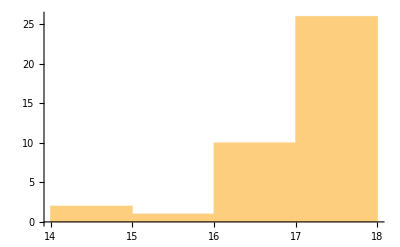

```mathematica
exSNRealization=snYearRealization[12,18,.48,typeIIFraction*subtypeFraction];
Histogram[exSNRealization]
```

### Optimization

##### Parameters

```mathematica
H0=70; (*70 km/s per Mpc*)
t0=6; (*6 hr observation time*)
(*σDOverD0StageII=10^-1;*)(*Standard devation in distance measurment in Mpc for observing a standard SN for 6 hr at 10 Mpc*)
σv0=250;(*Standard devation in redshift velocity measurment in km/s for observing a SN*)
D0=1; (*1 Mpc for normalization*)
MSNII=-16.1;(*Type II absolute magnitude. From Nearby Supernova Rates from the Lick Observatory Supernova Search by Fillipenko and others*)
MSNIa=-18.5;(*Type Ia absolute magnitude. From Nearby Supernova Rates from the Lick Observatory Supernova Search by Fillipenko and others*)
```

```mathematica
σtIII=3; (*Subscript[σ, t] for phase III in ps*)
σtII=10; (*Subscript[σ, t] for phase II in ps*)
RIII=2*10^4; (*Spectral resolution for phase III*)
RII=1*10^4;(*Spectral resolution for phase II*)
nIII=10;(*Number pair arrays for phase III*)
nII=1;(*Number pair arrays for phase II*)

telescopeRadiusII=5;(*Telescope radius in meters of phase II*)
telescopeRadiusIII=5;(*Telescope radius in meters of phase III*)

efficiencyFactor=1/2;

figureOfMerit[σtps_,Rspectral_,nArr_,telescopeRadius_,efficiency_]:=σtps^(-1/2)Rspectral^(1/2)nArr*(π*telescopeRadius^2)*efficiency
```

```mathematica
figureOfMeritStnd=figureOfMerit[σtII,RII,nII,telescopeRadiusII,efficiencyFactor]//N
```

1241.82

```mathematica
matchLightLow=500;
```

```mathematica
matchLightStnd=figureOfMeritStnd
```

1241.82

```mathematica
matchLightMidRange=10*matchLightStnd
```

12418.2

```mathematica
matchLightSuper=matchLightMidRange/matchLightLow*matchLightMidRange
```

308425.

```mathematica
lowMatchlightPaper=1250;
highMatchlightPaper=5*10^4;
```

```mathematica
σDoverDt0[m_,snrEnhancement_]:=6.3*10^-2*10^(0.4(m-12.0))*1/snrEnhancement
```

```mathematica
Dofm[m_,MSN_]:=D0*10^((m-MSN-25)/5)
```

```mathematica
σvSNTypeII[m_]:=σv0/(H0*Dofm[m,MSNII])
```

```mathematica
σvSNTypeIa[m_]:=σv0/(H0*Dofm[m,MSNIa])
```

```mathematica
t0hr=6;
```

```mathematica
oneσLowerQuantile=.5-.341
oneσUpperQuantile=.5+.341
```

0.159

0.841

##### Cosmic Variance Uncertainties

```mathematica
cvTab=Import[NotebookDirectory[]<>"Data/σHGaussianTabDirect.txt","Table"]
```

{{1.,0.205956},{1.25893,0.194934},{1.58489,0.183787},{1.99526,0.172003},{2.51189,0.159976},{3.16228,0.148831},{3.98107,0.137093},{5.01187,0.126815},{6.30957,0.117149},{7.94328,0.108029},{10.,0.099638},{12.5893,0.0901508},{15.8489,0.0800472},{19.9526,0.0683428},{25.1189,0.0558574},{31.6228,0.0449259},{39.8107,0.0345942},{50.1187,0.0267378},{63.0957,0.0203583},{79.4328,0.015258},{100.,0.0114443},{125.893,0.00817182},{158.489,0.0058368},{199.526,0.00410013},{251.189,0.00283243},{316.228,0.00195676},{398.107,0.00131842},{501.187,0.000888329},{630.957,0.000594127},{794.328,0.000278717},{1000.,0.000185077}}

```mathematica
logcvInterp=Interpolation[Log10[cvTab]]
```

InterpolatingFunction[…]

```mathematica
cvInterp[dMpch_]:=Evaluate[Power[10,logcvInterp[Log10[dMpch]]]]
```

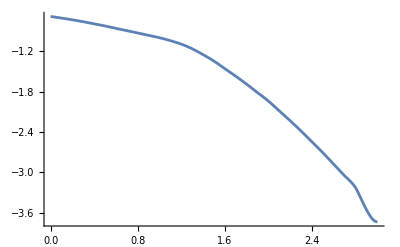

```mathematica
Plot[Log10[cvInterp[10^logdMpch]],{logdMpch,0,3}]
```

```mathematica
hHub=0.7;
fCVSNTypeIIOld[m_]:=0.2*(Dofm[m,MSNII]*hHub)^0.1*Exp[-(Log[(Dofm[m,MSNII]*hHub)^0.6]^2)/Log[10]]
```

```mathematica
fCVSNTypeII[m_]:=cvInterp[Dofm[m,MSNII]*hHub]
```

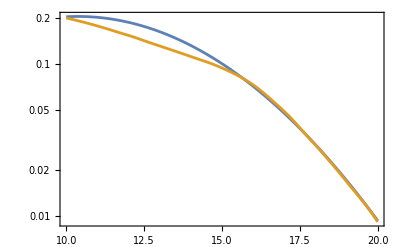

```mathematica
LogPlot[{fCVSNTypeIIOld[m],fCVSNTypeII[m]},{m,10,20},Frame->True,Axes->False,
BaseStyle->{FontSize->17,FontFamily->"Latin Modern Roman"},FrameLabel->{{MaTeX["\\sigma_{\\rm cv}
",Magnification->1.5],None},
{MaTeX["R \, [{\\rm Mpc}/h]",Magnification->1.5],None}}]
```

```mathematica
fCVSNTypeIaOld[m_]:=0.2*(Dofm[m,MSNIa]*hHub)^0.1*Exp[-(Log[(Dofm[m,MSNIa]*hHub)^0.6]^2)/Log[10]]
```

```mathematica
fCVSNTypeIa[m_]:=cvInterp[Dofm[m,MSNIa]*hHub]
```

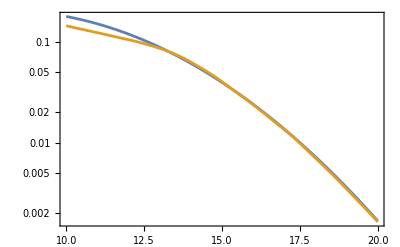

```mathematica
LogPlot[{fCVSNTypeIaOld[m],fCVSNTypeIa[m]},{m,10,20},Frame->True,Axes->False,
BaseStyle->{FontSize->17,FontFamily->"Latin Modern Roman"},FrameLabel->{{MaTeX["\\sigma_{\\rm cv}
",Magnification->1.5],None},
{MaTeX["R \, [{\\rm Mpc}/h]",Magnification->1.5],None}}]
```

#### SN Type II

##### Population IIP Trials

```mathematica
numTrials=(*1*)10(*25*)(*10*)(*500*);
numYrs=5;(*5*);
snPopulationTrialsTypeII=Table[Sort[
Flatten[Table[
snYearRealization[m0CDF,20.0(*19,*),b0CDF,typeIIFraction*subtypeFraction]
,{yrs,1,numYrs}]]
],{i,1,numTrials}];
```

##### Approximate max m for optimization

```mathematica
(*tstMaxmTabTypeII={{1,15.93},{10,17.2},{20,17.56},{30,17.78},{40,17.9},{100,18.4} } *)(*1 yr normalization*)(*Typical max mf vs snrEnhancement*)

tstMaxmTabTypeII={{0.1,16.41},{0.5,16.42},{1,16.516},{10,17.44},{20,17.765},{30,17.98},{40,18.135},{100,18.64},{500,19.474},{1000,19.856},{2000,19.995},{10000,19.995}(*,{600,19.36},{1000,19.626},{2000,19.99}*)}
```

{{0.1,16.41},{0.5,16.42},{1,16.516},{10,17.44},{20,17.765},{30,17.98},{40,18.135},{100,18.64},{500,19.474},{1000,19.856},{2000,19.995},{10000,19.995}}

```mathematica
tstMaxmTabTypeII=tstMaxmTabTypeII/.{x_,y_}->{x,y}
```

{{0.1,16.41},{0.5,16.42},{1,16.516},{10,17.44},{20,17.765},{30,17.98},{40,18.135},{100,18.64},{500,19.474},{1000,19.856},{2000,19.995},{10000,19.995}}

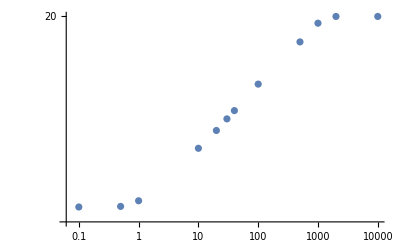

```mathematica
ListLogLogPlot[tstMaxmTabTypeII]
```

```mathematica
fitTypeII=NonlinearModelFit[Log10[tstMaxmTabTypeII],a*x+b,{a,b},x]
```

FittedModel[…]

```mathematica
fitTypeII["BestFit"]
```

1.22547+0.0213203 x

```mathematica
logmfMaxTypeIIa=Interpolation[Log10[tstMaxmTabTypeII],InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
mfMaxTypeII[snrEnhancement_]:=Evaluate[Power[10,logmfMaxTypeIIa[Log10[snrEnhancement]]]]
```

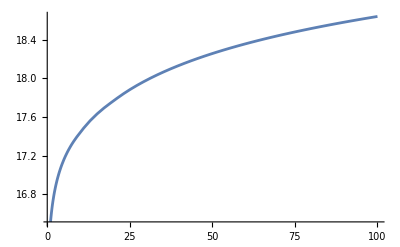

```mathematica
Plot[mfMaxTypeII[snrEnhancement],{snrEnhancement,1,100}]
```

##### Lagrange Multiplier Analysis (Stat only, no cosmic variance)

```mathematica
tiLangrangeMultiplierSNTypeII[inputSNList_,tTotalObservationhr_,snrEnhancement_]:=(
snPopList=inputSNList;
sum1UncertaintyRatio=Sum[(σDoverDt0[snPopList[[i]],snrEnhancement]/σvSNTypeII[snPopList[[i]]])^2 t0hr,{i,1,Length[snPopList]}];
sum2UncertaintyRatio=Sum[(σDoverDt0[snPopList[[i]],snrEnhancement]/σvSNTypeII[snPopList[[i]]]^2),{i,1,Length[snPopList]}];
tiIdealSNIITab=Table[
mi=snPopList[[i]];
ti=(tTotalObservationhr+sum1UncertaintyRatio)*(σDoverDt0[mi,snrEnhancement]/σvSNTypeII[mi]^2)/sum2UncertaintyRatio-(σDoverDt0[mi,snrEnhancement]/σvSNTypeII[mi])^2*t0hr;
{mi,ti},{i,1,Length[snPopList]}]
)
```

```mathematica
tiIdealSNTypeIIList[tTotalObservationhr_?NumericQ,snrEnhancement_,trialNum_:0,numOftPlateauSN_:0,fiducialNumSN_:-1,posOfBrightestSNTab_:1]:=(*(If[trialNum==0,snPop=Sort[snYearRealization[12,19,.48,typeIIFraction*subtypeFraction]],snPop=snPopulationTrialsTypeII[[trialNum]][[numOftPlateauSN+1;;fiducialNumSN]]];*)
(Which[trialNum==0,snPop=Sort[snYearRealization[m0CDF,19,b0CDF,typeIIFraction*subtypeFraction]],
fiducialNumSN===-1,snPop=snPopulationTrialsTypeII[[trialNum]][[1;;fiducialNumSN]],
True,snPop=Delete[snPopulationTrialsTypeII[[trialNum]],posOfBrightestSNTab][[1;;fiducialNumSN]]];
tiTimesPositiveDefinite=False;
snListLength=Length[snPop];
reducedSNPopList=snPop;
While[tiTimesPositiveDefinite===False,newtiTab=tiLangrangeMultiplierSNTypeII[reducedSNPopList,tTotalObservationhr,snrEnhancement];
observationTimeofBrightestSN=newtiTab[[-1]][[2]];
If[observationTimeofBrightestSN<=0,reducedSNPopList=Drop[reducedSNPopList,-1];,tiTimesPositiveDefinite=True];];
newtiTab)
```

```mathematica
σDoverDt[m_,snrEnhancement_,t_]:=σDoverDt0[m,snrEnhancement]*(t/t0hr)^(-1/2)
```

```mathematica
σμSNTypeII[inputSNList_,snrEnhancement_]:=(
snPopList=inputSNList;
σμIdealSNTypeII=(Sum[1/((σDoverDt[snPopList[[i,1]],snrEnhancement,snPopList[[i,2]]])^2+σvSNTypeII[snPopList[[i,1]]]^2),{i,1,Length[snPopList]}])^(-1/2)
)
```

```mathematica
σCVSNTypeII[inputSNList_]:=(
snPopList=inputSNList;
totObsTime=Sum[snPopList[[i,2]],{i,1,Length[snPopList]}];
σCVIdealSNTypeII=(Sum[snPopList[[i,2]]/totObsTime*fCVSNTypeII[snPopList[[i,1]]]^2,{i,1,Length[snPopList]}])^(1/2)
)
```

```mathematica
tPlateauTypeII=3*30*6;
numOftPlateauSN=0;
```

```mathematica
(*redoIdealσμHistogramSNTypeII[inputSNList_,snrEnhancement_,trialNum_]:=Module[{snPopList=inputSNList},
(
(*tObsOfBrightestSN=snPopList[[1,2]];*)
tObsOfBrightestSN=Max[snPopList[[;;,2]]];
totalObsTimeForOptimization=Sum[snPopList[[i,2]],{i,1,Length[snPopList]}];
numOfFiducialSN=Length[snPopList];
numOftPlateauSN=0;
updatedtiIdealSNTypeIIList=snPopList;
While[tObsOfBrightestSN>tPlateauTypeII,
numOftPlateauSN=numOftPlateauSN+1;
updatedtiIdealSNTypeIIList=tiIdealSNTypeIIList[totalObsTimeForOptimization-tPlateauTypeII,snrEnhancement,trialNum,numOftPlateauSN,numOfFiducialSN+30];
(*tObsOfBrightestSN=updatedtiIdealCepheidsList[[1,2]];*)
tObsOfBrightestSN=Max[updatedtiIdealSNTypeIIList[[;;,2]]];
totalObsTimeForOptimization=Sum[updatedtiIdealSNTypeIIList[[i,2]],{i,1,Length[updatedtiIdealSNTypeIIList]}];
numOfFiducialSN=Length[updatedtiIdealSNTypeIIList];
];
plateauSNTab=Table[{snPopulationTrialsTypeII[[trialNum,i]],tPlateauTypeII},{i,1,numOftPlateauSN}];
Join[plateauSNTab,updatedtiIdealSNTypeIIList]
(*{snPopList,updatedtiIdealCepheidsList}*)
)]*)

redoIdealσμHistogramSNTypeII[inputSNList_,snrEnhancement_,trialNum_]:=Module[{snPopList=inputSNList},
(
(*tObsOfBrightestSN=snPopList[[1,2]];*)
tObsOfBrightestSN=Max[snPopList[[;;,2]]];
posOfBrightestSN=Position[snPopList[[All,2]],tObsOfBrightestSN][[1,1]];
mOfBrightestSN=snPopList[[posOfBrightestSN,1]];
posOfBrightestSNMainList=Position[snPopulationTrialsTypeII[[trialNum]],mOfBrightestSN][[1,1]];

totalObsTimeForOptimization=Sum[snPopList[[i,2]],{i,1,Length[snPopList]}];
numOfFiducialSN=Length[snPopList];
numOftPlateauSN=0;
posOfPlateauSNTab={};
updatedtiIdealSNTypeIIList=snPopList;
While[tObsOfBrightestSN>tPlateauTypeII,
numOftPlateauSN=numOftPlateauSN+1;
posOfPlateauSNTab=Append[posOfPlateauSNTab,{posOfBrightestSNMainList}];
updatedtiIdealSNTypeIIList=tiIdealSNTypeIIList[totalObsTimeForOptimization-tPlateauTypeII,snrEnhancement,trialNum,numOftPlateauSN,numOfFiducialSN+30,posOfPlateauSNTab];
(*tObsOfBrightestSN=updatedtiIdealCepheidsList[[1,2]];*)
tObsOfBrightestSN=Max[updatedtiIdealSNTypeIIList[[;;,2]]];
posOfBrightestSNUpdatedList=Position[updatedtiIdealSNTypeIIList[[All,2]],tObsOfBrightestSN][[1,1]];
mOfBrightestSN=updatedtiIdealSNTypeIIList[[posOfBrightestSNUpdatedList,1]];
posOfBrightestSNMainList=Position[snPopulationTrialsTypeII[[trialNum]],mOfBrightestSN][[1,1]];
totalObsTimeForOptimization=Sum[updatedtiIdealSNTypeIIList[[i,2]],{i,1,Length[updatedtiIdealSNTypeIIList]}];
numOfFiducialSN=Length[updatedtiIdealSNTypeIIList];
];
(*plateauSNTab=Table[{snPopulationTrialsTypeII[[trialNum,i]],tPlateauTypeII},{i,1,numOftPlateauSN}];*)
plateauSNTab=Table[{snPopulationTrialsTypeII[[trialNum,i]],tPlateauTypeII},{i,Flatten[posOfPlateauSNTab]}];
Sort[Join[plateauSNTab,updatedtiIdealSNTypeIIList]]
(*{snPopList,updatedtiIdealCepheidsList}*)
)]
```

```mathematica
(*idealσμHistogramSNTypeII[tTotalObservationhr_?NumericQ,snrEnhancement_,trialNum_:0]:=(
Table[
(*idealSNPopulation=tiIdealCepheidsList[tTotalObservationhr,snrEnhancement,0];*)
idealSNPopulation=tiIdealSNTypeIIList[tTotalObservationhr,snrEnhancement,i];
idealSNPopulationPlateau=redoIdealσμHistogramSNTypeII[idealSNPopulation,snrEnhancement,i];
(*σμSNTypeII[(*idealSNPopulation*)idealSNPopulationPlateau,snrEnhancement],*)
{
σμSNTypeII[(*idealSNPopulation*)idealSNPopulationPlateau,snrEnhancement],
σCVSNTypeII[idealSNPopulationPlateau]},
{i,1,numTrials}]
)*)

idealσμHistogramSNTypeII[tTotalObservationhr_?NumericQ,snrEnhancement_,trialNum_:0]:=(
Table[
expectedMaxmf=mfMaxTypeII[snrEnhancement];
bufferNumSN=30;
maxNumSNToConsider=Min[Last[Position[snPopulationTrialsTypeII[[i]],x_/;x<expectedMaxmf]][[1]]+bufferNumSN,Length[snPopulationTrialsTypeII[[i]]]-1];
idealSNPopulation=tiIdealSNTypeIIList[tTotalObservationhr,snrEnhancement,i,0,maxNumSNToConsider];
idealSNPopulationPlateau=redoIdealσμHistogramSNTypeII[idealSNPopulation,snrEnhancement,i];
(*σμSNTypeII[(*idealSNPopulation*)idealSNPopulationPlateau,snrEnhancement],*)
{
σμSNTypeII[(*idealSNPopulation*)idealSNPopulationPlateau,snrEnhancement],
σCVSNTypeII[idealSNPopulationPlateau]},
{i,1,numTrials}]
)
```

#### SN Type Ia

##### Population Ia Trials

```mathematica
numTrials=10(*50*)(*500*);
numYrs=5;(*5;*)
snPopulationTrialsTypeIa=Table[Sort[
Flatten[Table[
snYearRealization[m0CDF,(*18*)20.0,b0CDF,typeIaFraction]
,{yrs,1,numYrs}]]
],{i,1,numTrials}];
```

##### Approximate max m for optimization

```mathematica
(*tstMaxmTab={{1,14.92},{10,16.18},{20,16.5},{30,16.75},{40,16.9}} *) (*Typical max mf vs snrEnhancement*) (*1 year*)
```

```mathematica
tstMaxmTab={{.1,14.56},{.3,14.63},{.5,14.73},{1,14.99},{10,16.2},{20,16.536},{30,16.75},{40,16.90},{100,17.379},{200,17.73},{400,18.0821},{1000,18.56},{2000,18.915},{5000,19.39},{10000,19.7503}}
```

{{0.1,14.56},{0.3,14.63},{0.5,14.73},{1,14.99},{10,16.2},{20,16.536},{30,16.75},{40,16.9},{100,17.379},{200,17.73},{400,18.0821},{1000,18.56},{2000,18.915},{5000,19.39},{10000,19.7503}}

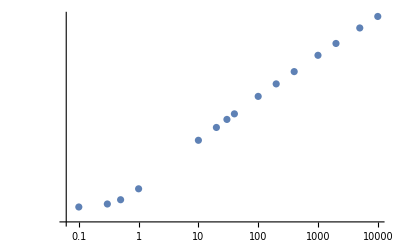

```mathematica
ListLogLogPlot[tstMaxmTab]
```

```mathematica
fitTypeIa=NonlinearModelFit[Log10[tstMaxmTab],a*x+b,{a,b},x]
```

FittedModel[…]

```mathematica
fitTypeIa["BestFit"]
```

1.1818+0.0286101 x

```mathematica
bufferM=0;
(*mfMaxTypeIa[snrEnhancement_]:=Max[10^(1.17724+0.0308*Log10[snrEnhancement])+bufferM,14]*)
```

```mathematica
logmfMaxTypeIa=Interpolation[Log10[tstMaxmTab],InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
mfMaxTypeIa[snrEnhancement_]:=Evaluate[Power[10,logmfMaxTypeIa[Log10[snrEnhancement]]]]
```

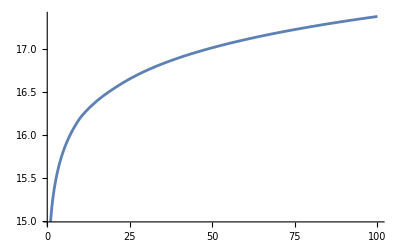

```mathematica
Plot[mfMaxTypeIa[snrEnhancement],{snrEnhancement,1,100}]
```

##### Lagrange Multiplier Analysis (Stat only, no cosmic variance)

```mathematica
tiLangrangeMultiplierSNTypeIa[inputSNList_,tTotalObservationhr_,snrEnhancement_]:=(
snPopList=inputSNList;
sum1UncertaintyRatio=Sum[(σDoverDt0[snPopList[[i]],snrEnhancement]/σvSNTypeIa[snPopList[[i]]])^2 t0hr,{i,1,Length[snPopList]}];
sum2UncertaintyRatio=Sum[(σDoverDt0[snPopList[[i]],snrEnhancement]/σvSNTypeIa[snPopList[[i]]]^2),{i,1,Length[snPopList]}];
tiIdealSNIITab=Table[
mi=snPopList[[i]];
ti=(tTotalObservationhr+sum1UncertaintyRatio)*(σDoverDt0[mi,snrEnhancement]/σvSNTypeIa[mi]^2)/sum2UncertaintyRatio-(σDoverDt0[mi,snrEnhancement]/σvSNTypeIa[mi])^2*t0hr;
{mi,ti},{i,1,Length[snPopList]}]
)
```

```mathematica
tiIdealSNTypeIaList[tTotalObservationhr_?NumericQ,snrEnhancement_,trialNum_:0,numOftPlateauSN_:0,fiducialNumSN_:-1,posOfBrightestSNTab_:1]:=(*(If[trialNum==0,snPop=Sort[snYearRealization[12,19,.48,TypeIaFraction*subtypeFraction]],snPop=snPopulationTrialsTypeIa[[trialNum]][[numOftPlateauSN+1;;fiducialNumSN]]];*)
(Which[trialNum==0,snPop=Sort[snYearRealization[m0CDF,19,b0CDF,typeIaFraction]],fiducialNumSN===-1,snPop=snPopulationTrialsTypeIa[[trialNum]][[1;;fiducialNumSN]],True,snPop=Delete[snPopulationTrialsTypeIa[[trialNum]],posOfBrightestSNTab][[1;;fiducialNumSN]]];
tiTimesPositiveDefinite=False;
snListLength=Length[snPop];
reducedSNPopList=snPop;
While[tiTimesPositiveDefinite===False,newtiTab=tiLangrangeMultiplierSNTypeIa[reducedSNPopList,tTotalObservationhr,snrEnhancement];
observationTimeofBrightestSN=newtiTab[[-1]][[2]];
If[observationTimeofBrightestSN<=0,reducedSNPopList=Drop[reducedSNPopList,-1];,tiTimesPositiveDefinite=True];];
newtiTab)
```

```mathematica
σDoverDt[m_,snrEnhancement_,t_]:=σDoverDt0[m,snrEnhancement]*(t/t0hr)^(-1/2)
```

```mathematica
σμSNTypeIa[inputSNList_,snrEnhancement_]:=(
snPopList=inputSNList;
σμIdealSNTypeIa=(Sum[1/((σDoverDt[snPopList[[i,1]],snrEnhancement,snPopList[[i,2]]])^2+σvSNTypeIa[snPopList[[i,1]]]^2),{i,1,Length[snPopList]}])^(-1/2)
)
```

```mathematica
σCVSNTypeIa[inputSNList_]:=(
snPopList=inputSNList;
totObsTime=Sum[snPopList[[i,2]],{i,1,Length[snPopList]}];
σCVIdealSNTypeIa=Sum[snPopList[[i,2]]/totObsTime*fCVSNTypeIa[snPopList[[i,1]]]^2,{i,1,Length[snPopList]}]^(1/2)
)
```

```mathematica
tPlateauTypeIa=1*30*6;
numOftPlateauSN=0;
```

```mathematica
(*redoIdealσμHistogramSNTypeIa[inputSNList_,snrEnhancement_,trialNum_]:=Module[{snPopList=inputSNList},
(
(*tObsOfBrightestSN=snPopList[[1,2]];*)
tObsOfBrightestSN=Max[snPopList[[;;,2]]];
totalObsTimeForOptimization=Sum[snPopList[[i,2]],{i,1,Length[snPopList]}];
numOfFiducialSN=Length[snPopList];
numOftPlateauSN=0;
updatedtiIdealSNTypeIaList=snPopList;
While[tObsOfBrightestSN>tPlateauTypeIa,
numOftPlateauSN=numOftPlateauSN+1;
updatedtiIdealSNTypeIaList=tiIdealSNTypeIaList[totalObsTimeForOptimization-tPlateauTypeIa,snrEnhancement,trialNum,numOftPlateauSN,numOfFiducialSN+30];
(*tObsOfBrightestSN=updatedtiIdealCepheidsList[[1,2]];*)
tObsOfBrightestSN=Max[updatedtiIdealSNTypeIaList[[;;,2]]];
totalObsTimeForOptimization=Sum[updatedtiIdealSNTypeIaList[[i,2]],{i,1,Length[updatedtiIdealSNTypeIaList]}];
numOfFiducialSN=Length[updatedtiIdealSNTypeIaList];
];
plateauSNTab=Table[{snPopulationTrialsTypeIa[[trialNum,i]],tPlateauTypeIa},{i,1,numOftPlateauSN}];
Join[plateauSNTab,updatedtiIdealSNTypeIaList]
(*{snPopList,updatedtiIdealCepheidsList}*)
)]*)

redoIdealσμHistogramSNTypeIa[inputSNList_,snrEnhancement_,trialNum_]:=Module[{snPopList=inputSNList},
(
(*tObsOfBrightestSN=snPopList[[1,2]];*)
tObsOfBrightestSN=Max[snPopList[[;;,2]]];
posOfBrightestSN=Position[snPopList[[All,2]],tObsOfBrightestSN][[1,1]];
mOfBrightestSN=snPopList[[posOfBrightestSN,1]];
posOfBrightestSNMainList=Position[snPopulationTrialsTypeIa[[trialNum]],mOfBrightestSN][[1,1]];

totalObsTimeForOptimization=Sum[snPopList[[i,2]],{i,1,Length[snPopList]}];
numOfFiducialSN=Length[snPopList];
numOftPlateauSN=0;
posOfPlateauSNTab={};
updatedtiIdealSNTypeIaList=snPopList;
While[tObsOfBrightestSN>tPlateauTypeIa,
numOftPlateauSN=numOftPlateauSN+1;
posOfPlateauSNTab=Append[posOfPlateauSNTab,{posOfBrightestSNMainList}];
updatedtiIdealSNTypeIaList=tiIdealSNTypeIaList[totalObsTimeForOptimization-tPlateauTypeIa,snrEnhancement,trialNum,numOftPlateauSN,numOfFiducialSN+30,posOfPlateauSNTab];
(*tObsOfBrightestSN=updatedtiIdealCepheidsList[[1,2]];*)
tObsOfBrightestSN=Max[updatedtiIdealSNTypeIaList[[;;,2]]];
posOfBrightestSNUpdatedList=Position[updatedtiIdealSNTypeIaList[[All,2]],tObsOfBrightestSN][[1,1]];
mOfBrightestSN=updatedtiIdealSNTypeIaList[[posOfBrightestSNUpdatedList,1]];
posOfBrightestSNMainList=Position[snPopulationTrialsTypeIa[[trialNum]],mOfBrightestSN][[1,1]];
totalObsTimeForOptimization=Sum[updatedtiIdealSNTypeIaList[[i,2]],{i,1,Length[updatedtiIdealSNTypeIaList]}];
numOfFiducialSN=Length[updatedtiIdealSNTypeIaList];
];
(*plateauSNTab=Table[{snPopulationTrialsTypeIa[[trialNum,i]],tPlateauTypeIa},{i,1,numOftPlateauSN}];*)
plateauSNTab=Table[{snPopulationTrialsTypeIa[[trialNum,i]],tPlateauTypeIa},{i,Flatten[posOfPlateauSNTab]}];
Sort[Join[plateauSNTab,updatedtiIdealSNTypeIaList]]
(*{snPopList,updatedtiIdealCepheidsList}*)
)]
```

```mathematica
(*idealσμHistogramSNTypeIa[tTotalObservationhr_?NumericQ,snrEnhancement_,trialNum_:0]:=(
Table[
(*idealSNPopulation=tiIdealCepheidsList[tTotalObservationhr,snrEnhancement,0];*)
expectedMaxmf=mfMax[snrEnhancement];
maxNumSNToConsider=Last[Position[snPopulationTrialsTypeIa[[i]],x_/;x<expectedMaxmf]][[1]];
idealSNPopulation=tiIdealSNTypeIaList[tTotalObservationhr,snrEnhancement,i,0,maxNumSNToConsider];
idealSNPopulationPlateau=redoIdealσμHistogramSNTypeIa[idealSNPopulation,snrEnhancement,i];
(*σμSNTypeIa[(*idealSNPopulation*)idealSNPopulationPlateau,snrEnhancement],*)
{σμSNTypeIa[(*idealSNPopulation*)idealSNPopulationPlateau,snrEnhancement],σCVSNTypeIa[idealSNPopulationPlateau]},
{i,1,numTrials}]
)*)

idealσμHistogramSNTypeIa[tTotalObservationhr_?NumericQ,snrEnhancement_,trialNum_:0]:=(
Table[
expectedMaxmf=mfMaxTypeIa[snrEnhancement];(*expectedMaxmf=18.2;*)
bufferNumSN=100;
maxNumSNToConsider=Min[Last[Position[snPopulationTrialsTypeIa[[i]],x_/;x<expectedMaxmf]][[1]]+bufferNumSN,Length[snPopulationTrialsTypeIa[[i]]]-1];
idealSNPopulation=tiIdealSNTypeIaList[tTotalObservationhr,snrEnhancement,i,0,maxNumSNToConsider];
idealSNPopulationPlateau=redoIdealσμHistogramSNTypeIa[idealSNPopulation,snrEnhancement,i];
(*σμSNTypeII[(*idealSNPopulation*)idealSNPopulationPlateau,snrEnhancement],*)
{
σμSNTypeIa[(*idealSNPopulation*)idealSNPopulationPlateau,snrEnhancement],
σCVSNTypeIa[idealSNPopulationPlateau]},
{i,1,numTrials}]
)
```

### Population Example FWHM

##### Type II P Example Population

```mathematica
snrEnhancementTabPopulation=Table[10^logmatchlight*1/matchLightStnd,{logmatchlight,3,6,1/3}]
```

{0.805267,1.7349,3.73772,8.05267,17.349,37.3772,80.5267,173.49,373.772,805.267}

```mathematica
typeIIPPopulationTab=ParallelTable[
idealSNPopulation=tiIdealSNTypeIIList[365*6*numYrs,snrEnhancementIterator,2];
idealSNPopulationPlateau=redoIdealσμHistogramSNTypeII[idealSNPopulation,snrEnhancementIterator,2],{snrEnhancementIterator,snrEnhancementTabPopulation}];
```

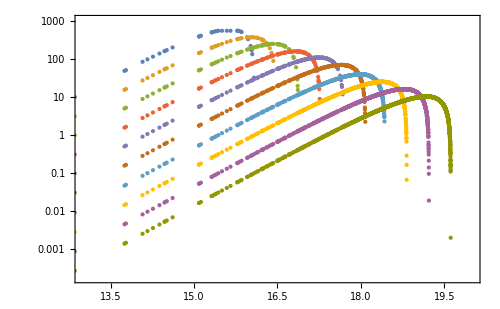

```mathematica
tObsAllocationSNTypeIIPlot=ListLogPlot[typeIIPPopulationTab,
PlotStyle->AbsolutePointSize[3],
Frame->True,Axes->False,
BaseStyle->{FontSize->17,FontFamily->"Latin Modern Roman"},
PlotRange->{{13,20},{10^-3.75,1000}},
(*FrameTicks->{{logTick[-3,3,1.5,1],logTickNone[-3,3,1.5,1]},{logTick[2,6,1.5,1],None}},*)FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],FrameLabel->{{MaTeX["t_{{\\rm obs},i}
\\text{ [hr] (SN Observation Time)}
",Magnification->1.5],None},
{MaTeX["m_i \\text{ (SN Apparent Magnitude)}",Magnification->1.5],None}},ImageSize->500]
```

```mathematica
Table[Variance[typeIIPPopulationTab[[i]]],{i,1,Length[typeIIPPopulationTab]}]
```

{{0.660057,38588.4},{0.731516,14922.7},{0.794066,7346.8},{0.830686,2728.67},{0.859301,1304.22},{0.893377,500.311},{0.840474,154.636},{0.803429,68.2421},{0.783041,27.0632},{0.771751,10.7815}}

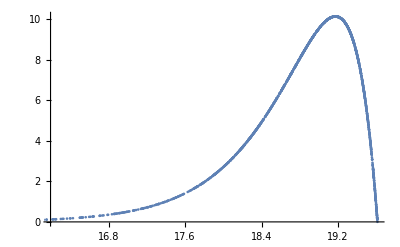

```mathematica
ListPlot[typeIIPPopulationTab[[10]]]
```

```mathematica
tObsAllocationSNTypeIIPlotLine=ListLogPlot[typeIIPPopulationTab,
PlotStyle->{{AbsoluteThickness[2],Opacity[.1]}},
Frame->True,Axes->False,
Joined->True,
BaseStyle->{FontSize->17,FontFamily->"Latin Modern Roman"},
PlotRange->{{13,20},{10^-3.75,1000}},
(*FrameTicks->{{logTick[-3,3,1.5,1],logTickNone[-3,3,1.5,1]},{logTick[2,6,1.5,1],None}},*)FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],FrameLabel->{{MaTeX["t_{{\\rm obs},i}
\\text{ [hr] (SN Observation Time)}
",Magnification->1.5],None},
{MaTeX["m_i \\text{ (SN Apparent Magnitude)}",Magnification->1.5],None}},ImageSize->500,
Epilog->{
Inset[Rotate[Framed[Style[Rotate[changeStyle[Darker[color[10],.3]]@MaTeX["10^6",Magnification->1.1],0Degree]],Background->Directive[White,Opacity[.75]],FrameStyle->None,FrameMargins->{{None,None},{-4,-4}}],27.5Degree],Scaled[{.26-.123,.195-.04}]],
Inset[Rotate[Framed[Style[Rotate[changeStyle[Darker[color[7],.3]]@MaTeX[" 10^5",Magnification->1.1]]],Background->Directive[White,Opacity[.5]],FrameStyle->None,FrameMargins->{{None,None},{-3,-3}}],27.5Degree],Scaled[{.26-.123,.21+.3-.0625+.045-.1}]],
Inset[Rotate[Framed[Style[Rotate[changeStyle[Darker[color[4],.3]]@MaTeX[" 10^4",Magnification->1.1],0Degree]],Background->Directive[White,Opacity[.5]],FrameStyle->None,FrameMargins->{{None,None},{-3,-3}}],27.5Degree],Scaled[{.26-.123,.21+.51-.0625+.055-.1}]],
Inset[Rotate[Framed[Style[Rotate[changeStyle[Darker[color[1],.3]]@MaTeX["\\text{Matchlight = } 10^3",Magnification->1.1],0Degree]],Background->Directive[White,Opacity[0]],FrameStyle->None,FrameMargins->{{None,None},{-3,-3}}],24Degree],Scaled[{.26-.1,.21+.72-.0625+.01+.045-.05}]]
}]
```

-Graphics-

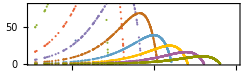

```mathematica
tObsAllocationSNTypeIIZoomPlot=ListPlot[typeIIPPopulationTab,
(*Joined->True,*)
(*Mesh->All,*)
(*MeshStyle->{AbsolutePointSize[4]},*)
PlotStyle->AbsolutePointSize[1.5],
Frame->True,Axes->False,PlotRange->{{15,20},{0,80}},
BaseStyle->{FontSize->12,FontFamily->"Latin Modern Roman"},
(*FrameTicks->{{logTick[-3,3,1.5,1],logTickNone[-3,3,1.5,1]},{logTick[2,6,1.5,1],None}},*)FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],(*FrameLabel->{{MaTeX["t_{{\\rm obs},i}
\\text{ [hr] (SN Observation Time)}
",Magnification->1.0],None},
{MaTeX["m_i \\text{ (SN Apparent Magnitude)}",Magnification->1.5],None}},*)ImageSize->250,AspectRatio->1/3.5]
```

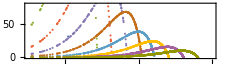
-Graphics--Graphics--Graphics-

```mathematica
combinedtObsAllocationExamplePlot=Overlay[{tObsAllocationSNTypeIIPlot, tObsAllocationSNTypeIIPlotLine,Item[Show[tObsAllocationSNTypeIIZoomPlot, ImageSize -> 225], Alignment -> {.185, -.2}]}]
```

```mathematica
Export[NotebookDirectory[]<>"Figures/combinedtObsAllocationExamplePlot.pdf",combinedtObsAllocationExamplePlot]
```

/Users/david/Documents/Projects/EPIC Hubble/Github Code/Figures/combinedtObsAllocationExamplePlot.pdf

### Numeric Minimization Covariance Matrix

#### Type IIP

##### Analysis

```mathematica
snrEnhancementTab=Table[10^logSNREnhancement,{logSNREnhancement,-.1,2,.1}]
```

{0.794328,1.,1.25893,1.58489,1.99526,2.51189,3.16228,3.98107,5.01187,6.30957,7.94328,10.,12.5893,15.8489,19.9526,25.1189,31.6228,39.8107,50.1187,63.0957,79.4328,100.}

```mathematica
coarseTab=(*{1/8}*)Table[(1/2)^i,{i,1,2}]
```

{1/2,1/4}

```mathematica
findZeroCoarsenessσHoverH[dataTab_]:=(
fit=NonlinearModelFit[dataTab,a*x+b,{a,b},x];
fitFunction=Normal[fit];
intercept=fitFunction/.{x->0}
)
```

```mathematica
findPeakTypeIIDistance[inputCoarseSNList_,timeTab_,timeSol_]:=(
timeTabSol=timeTab/.minSol[[2]];
tObsSolTab=Table[{inputCoarseSNList[[i,1]],timeTabSol[[i]]*inputCoarseSNList[[i,2]]},{i,1,Length[inputCoarseSNList]}];

peakObsTime=Max[tObsSolTab[[All,2]]];
peakObsTimePos=Last[Position[tObsSolTab[[All,2]],peakObsTime]][[1]];
peakApparentMag=tObsSolTab[[peakObsTimePos,1]];
peakDistanceII=Dofm[peakApparentMag,MSNII]
)
```

```mathematica
numericalMinimizationTypeII[inputSNList_,totalObsTime_,snrEnhancement_]:=(
snPopList=inputSNList;
coarseVSσHOverHTab=Table[
coarseSNPopTab=Round[snPopList,coarseTab[[i]]];
gatherTab=Gather[coarseSNPopTab][[1;;-1]];
lengthCoarseTab=Table[{gatherTab[[i,1]],Length[gatherTab[[i]]]},{i,1,Length[gatherTab]}];
timeTab=Table[ToExpression["t"<>ToString[i]],{i,1,Length[lengthCoarseTab]}];
sumTimeTab=Sum[timeTab[[i]]*lengthCoarseTab[[i,2]],{i,1,Length[timeTab]}]==totalObsTime;
inequalityTimeTab=Table[timeTab[[i]]>10^-8,{i,1,Length[timeTab]}];
constraints=Flatten[{sumTimeTab,inequalityTimeTab}];

lagrangianNumerator=1+Sum[(lengthCoarseTab[[i,2]]*fCVSNTypeII[lengthCoarseTab[[i,1]]]^2)/(σDoverDt[lengthCoarseTab[[i,1]],snrEnhancement,timeTab[[i]]]^2+σvSNTypeII[lengthCoarseTab[[i,1]]]^2),{i,1,Length[lengthCoarseTab]}];

lagrangianDenominatorSum1=Sum[lengthCoarseTab[[i,2]]/(σDoverDt[lengthCoarseTab[[i,1]],snrEnhancement,timeTab[[i]]]^2+σvSNTypeII[lengthCoarseTab[[i,1]]]^2),{i,1,Length[lengthCoarseTab]}];

lagrangianDenominatorSum2=Sum[(lengthCoarseTab[[i,2]]/(σDoverDt[lengthCoarseTab[[i,1]],snrEnhancement,timeTab[[i]]]^2+σvSNTypeII[lengthCoarseTab[[i,1]]]^2))*(lengthCoarseTab[[j,2]]/(σDoverDt[lengthCoarseTab[[j,1]],snrEnhancement,timeTab[[j]]]^2+σvSNTypeII[lengthCoarseTab[[j,1]]]^2))*(fCVSNTypeII[lengthCoarseTab[[i,1]]]-fCVSNTypeII[lengthCoarseTab[[j,1]]])^2,
{i,1,Length[lengthCoarseTab]},{j,1,Length[lengthCoarseTab]}];

lagrangian=√(lagrangianNumerator/(lagrangianDenominatorSum1+lagrangianDenominatorSum2));

minSol=NMinimize[{lagrangian,constraints},timeTab,Method->"SimulatedAnnealing"(*,AccuracyGoal->6*)(*6*)];
minσHoverHTot=minSol[[1]];
peakTypeIIDistance=findPeakTypeIIDistance[lengthCoarseTab,timeTab,minSol[[2]]];
{coarseTab[[i]],minσHoverHTot,peakTypeIIDistance}
,{i,1,Length[coarseTab]}];

σHOverHvsCoarsenessTab=coarseVSσHOverHTab[[All,1;;2]];
peakDistancevsCoarsenessTab=coarseVSσHOverHTab[[All,3]];

{findZeroCoarsenessσHoverH[σHOverHvsCoarsenessTab],Mean[peakDistancevsCoarsenessTab]}

)

numericalMinimizationTypeIIPopulation[totalObsTime_,snrEnhancement_]:=(
Table[
startingSNPop=snPopulationTrialsTypeII[[i]];
{numericalMinimizationTypeII[startingSNPop,totalObsTime,snrEnhancement]},
{i,1,numTrials}]
)
```

```mathematica
snrExample=(*40*)highMatchlightPaper/matchLightStnd
```

40.2634

```mathematica
numericalMinimizationTypeIIPopulation[365*6*numYrs,snrExample]
```

{{{0.0147405,70.1002}},{{0.0145926,70.1002}},{{0.0148418,70.1002}},{{0.0150126,70.1002}},{{0.0153005,70.1002}},{{0.0146015,70.1002}},{{0.0148576,70.1002}},{{0.0154256,70.1002}},{{0.0144958,70.1002}},{{0.0145668,70.1002}}}

```mathematica
minSol
```

{0.0146685,{t1→0.279684,t2→2.03729,t3→1.77614,t4→2.50243,t5→3.5864,t6→4.96934,t7→6.70725,t8→8.96073,t9→10.9218,t10→12.1586,t11→10.8113,t12→4.42804,t13→0.0596294,t14→0.0668463,t15→2.23054,t16→20.8703,t17→42.9223,t18→45.4552,t19→0.302503,t20→0.0159174,t21→0.00613746,t22→0.00303781,t23→0.00188954,t24→0.00117117,t25→0.00168809}}

```mathematica
timeTabSol=timeTab/.minSol[[2]]
```

{0.279684,2.03729,1.77614,2.50243,3.5864,4.96934,6.70725,8.96073,10.9218,12.1586,10.8113,4.42804,0.0596294,0.0668463,2.23054,20.8703,42.9223,45.4552,0.302503,0.0159174,0.00613746,0.00303781,0.00188954,0.00117117,0.00168809}

```mathematica
.0147
.0146
.0147
.0149
```

0.0147

0.0146

0.0147

0.0149

```mathematica
tObsSolTab=Table[{lengthCoarseTab[[i,1]],timeTabSol[[i]]*lengthCoarseTab[[i,2]]},{i,1,Length[lengthCoarseTab]}]
```

{{13,0.279684},{57/4,2.03729},{29/2,7.10455},{59/4,5.00485},{15,14.3456},{61/4,19.8774},{31/2,40.2435},{63/4,26.8822},{16,120.14},{65/4,121.586},{33/2,75.6793},{67/4,70.8487},{17,1.90814},{69/4,2.33962},{35/2,111.527},{71/4,1085.25},{18,3605.47},{73/4,5590.99},{37/2,40.5353},{75/4,3.21531},{19,1.52209},{77/4,1.03286},{39/2,0.818169},{79/4,0.714415},{20,0.646538}}

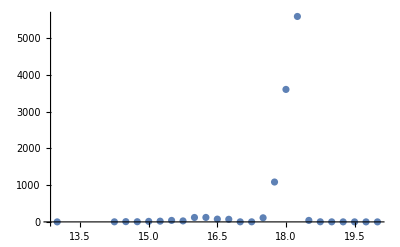

```mathematica
ListPlot[tObsSolTab,PlotRange->All]
```

```mathematica
fitGaussian=NonlinearModelFit[tObsSolTab,a*Exp[(-(m-μ)^2)/(2*σ^2)],{{μ,18.1},{σ,.1},a},m];
fitGaussian["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
μ | 18.1566 | 0.00809702 | 2242.38 | 1.8915×10^-60
σ | 0.139225 | 0.0142544 | 9.76715 | 1.85004×10^-9
a | 6935.92 | 593.708 | 11.6824 | 6.64317×10^-11

```mathematica
(*Export[NotebookDirectory[]<>"tObsSolTabDeltamWidth1Over8_updatedSNPop.m",tObsSolTab]*)
```

```mathematica
tObsSolTabDeltamWidth1Over2=Import[NotebookDirectory[]<>"Data/tObsSolTabDeltamWidth1Over2_updatedSNPop.m"];
tObsSolTabDeltamWidth1Over4=Import[NotebookDirectory[]<>"Data/tObsSolTabDeltamWidth1Over4_updatedSNPop.m"];
tObsSolTabDeltamWidth1Over8=Import[NotebookDirectory[]<>"Data/tObsSolTabDeltamWidth1Over8_updatedSNPop.m"];
```

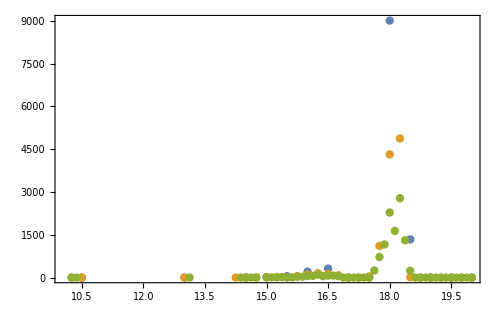

```mathematica
deltamComparisonPlot=ListPlot[{
tObsSolTabDeltamWidth1Over2,
tObsSolTabDeltamWidth1Over4,
tObsSolTabDeltamWidth1Over8
}
,PlotStyle->AbsolutePointSize[6]
(*PlotStyle->{color[1],,color[2],color[3],{color[4],Opacity[.85]}}*)
,PlotRange->All,Frame->True,BaseStyle->{FontSize->17,FontFamily->"Latin Modern Roman"},FrameLabel->{{MaTeX["t_{\\rm obs} \\, \\rm [hr]
",Magnification->1.5],None},
{MaTeX["m",Magnification->1.5],None}},ImageSize->500,
FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],FrameLabel->{{MaTeX["
\\sigma_{H_0}/H_0
",Magnification->1.75],None},{MaTeX["\\text{Interferometer Matchlight}",Magnification->1.75]
(*MaTeX["\\text{Matchlight }\\equiv [1 \\, \\rm{meter^2/picosecond^{1/2}}]",Magnification->1.5]*),None}},ImageSize->600,AspectRatio->1/GoldenRatio,(*1/2,*)ImagePadding->{{80,20},{70,70}},Epilog->{
(*Inset[Style[Rotate[changeStyle[Darker[Black,.3]]@MaTeX["\\text{Coarse-Grained Numerical Optimization}",Magnification->1.35],0 Degree]],Scaled[{.4,0.75}]]*)
}]
```

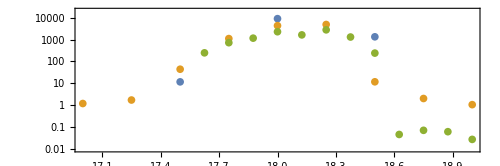

```mathematica
deltamComparisonLogPlot=ListLogPlot[{
tObsSolTabDeltamWidth1Over2,
tObsSolTabDeltamWidth1Over4,
tObsSolTabDeltamWidth1Over8
},
PlotStyle->{color[1],color[2],color[3],{color[4],Opacity[.85]}}
,PlotRange->{{17,19},{10^-2,2*10^4}},Frame->True,BaseStyle->{FontSize->17,FontFamily->"Latin Modern Roman"},FrameLabel->{{MaTeX["t_{\\rm obs} \\, \\rm [hr]
",Magnification->1.5],None},
{MaTeX["m",Magnification->1.5],None}},ImageSize->500,
FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],FrameLabel->{{MaTeX["
\\sigma_{H_0}/H_0
",Magnification->1.75],None},{MaTeX["\\text{Interferometer Matchlight}",Magnification->1.75]
(*MaTeX["\\text{Matchlight }\\equiv [1 \\, \\rm{meter^2/picosecond^{1/2}}]",Magnification->1.5]*),None}},ImageSize->600,AspectRatio->1/3,(*1/2,*)ImagePadding->{{80,20},{70,70}}]
```

##### Fitted Lines

```mathematica
fit1Over2=NonlinearModelFit[tObsSolTabDeltamWidth1Over2,a*Exp[(-(m-μ)^2)/(2*σ^2)],{{μ,18.1},{σ,.1},a},m]
```

FittedModel[…]

```mathematica
fit1Over4=NonlinearModelFit[tObsSolTabDeltamWidth1Over4,a*Exp[(-(m-μ)^2)/(2*σ^2)],{{μ,18.1},{σ,.1},a},m]
```

FittedModel[…]

```mathematica
fit1Over8=NonlinearModelFit[tObsSolTabDeltamWidth1Over8,a*Exp[(-(m-μ)^2)/(2*σ^2)],{{μ,18.1},{σ,.1},a},m]
```

FittedModel[…]

FittedModel[…]

```mathematica
fit1Over2["ParameterTable"]
fit1Over4["ParameterTable"]
fit1Over8["ParameterTable"]
```

General::munfl: Exp[-997.673] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
μ | 18.1384 | 0.127812 | 141.915 | 2.66398×10^-19
σ | 0.171 | 0.0979038 | 1.74661 | 0.10853
a | 12495.7 | 12247.9 | 1.02023 | 0.329534

General::munfl: Exp[-1072.17] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1005.21] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1072.17] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
μ | 18.129 | 0.00618611 | 2930.59 | 3.65513×10^-68
σ | 0.170146 | 0.00967363 | 17.5887 | 3.23439×10^-15
a | 6024.61 | 265.041 | 22.7308 | 9.62806×10^-18

| Estimate | Standard Error | t-Statistic | P-Value
μ | 18.1302 | 0.0130774 | 1386.37 | 7.68059×10^-106
σ | -0.222578 | 0.0130774 | -17.02 | 3.13314×10^-21
a | 2384.07 | 121.309 | 19.653 | 1.02778×10^-23

```mathematica
fit1Over2Function[m_]:=Evaluate[Normal[fit1Over2]]
fit1Over4Function[m_]:=Evaluate[Normal[fit1Over4]]
fit1Over8Function[m_]:=Evaluate[Normal[fit1Over8]]
```

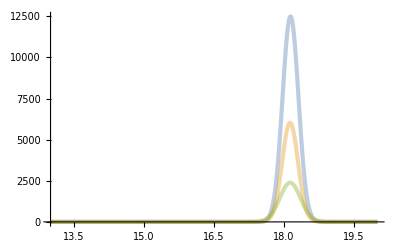

```mathematica
tstPlot=Plot[{fit1Over2Function[m],fit1Over4Function[m],fit1Over8Function[m](*,fit1Over16Function[m]*)},{m,13,20},PlotRange->All,PlotStyle->{{Opacity[.4],AbsoluteThickness[3]}}]
```

```mathematica
totaldeltamComparisonPlot=Show[deltamComparisonPlot,tstPlot,PlotRange->{{13,20},All},
Axes->False,
Epilog->{
Inset[Style[Rotate[changeStyle[Darker[color[1],.2]]@MaTeX["\\Delta m = 1/2",Magnification->1.25],0 Degree]],
Scaled[{.9-.65,.3+.215}]],
Inset[Style[Rotate[changeStyle[Darker[color[2],.2]]@MaTeX["\\Delta m = 1/4",Magnification->1.25],0 Degree]],
Scaled[{.9-.65,.3+.215-.085}]],
Inset[Style[Rotate[changeStyle[Darker[color[3],.2]]@MaTeX["\\Delta m = 1/8",Magnification->1.25],0 Degree]],
Scaled[{.9-.65,.3+.215-2*.085}]],
Inset[Style[Rotate[changeStyle[Darker[color[6],1]]@MaTeX["\\text{Coarse-Graining Optimization}",Magnification->1.6],0 Degree]],
Scaled[{.35,.9}]],
{Darker[color[1],0],AbsoluteThickness[3],Arrowheads[0],Arrow[{Scaled[{.775-.7,.3+.215}],Scaled[{.85-.7,.3+.215}]}]},
{Darker[color[2],0],AbsoluteThickness[3],Arrowheads[0],Arrow[{Scaled[{.775-.7,.3+.215-.085}],Scaled[{.85-.7,.3+.215-.085}]}]},
{Darker[color[3],0],AbsoluteThickness[3],Arrowheads[0],Arrow[{Scaled[{.775-.7,.3+.215-2*.085}],Scaled[{.85-.7,.3+.215-2*.085}]}]}
}]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"Figures/totaldeltamComparisonPlot.pdf",totaldeltamComparisonPlot]
```

/Users/david/Documents/Projects/EPIC Hubble/Github Code/Figures/totaldeltamComparisonPlot.pdf

##### Optimization vs Matchlight

```mathematica
σHoverHNumericalTypeIIvsMatchlight[tTotalObservationhr_?NumericQ]:=(
ParallelTable[
snrEnhancementIterator=snrEnhancementTab[[i]];
histogramNumericalTypeII=numericalMinimizationTypeIIPopulation[tTotalObservationhr,snrEnhancementIterator];
numericStatPlusSysTypeII=histogramNumericalTypeII[[All,1,1]];
numericPeakDistanceTypeII=histogramNumericalTypeII[[All,1,2]];
{Mean[numericStatPlusSysTypeII],Quantile[numericStatPlusSysTypeII,{oneσLowerQuantile,oneσUpperQuantile}],Mean[numericPeakDistanceTypeII]},{i,1,Length[snrEnhancementTab]}
])
```

```mathematica
(*Uncomment to run new realization*)
(*σHoverHNumericalTypeIIvsMatchlightTab=σHoverHNumericalTypeIIvsMatchlight[365*6*numYrs]*)
```

```mathematica
(*Export[NotebookDirectory[]<>"Data/σHoverHNumericalTypeIIvsMatchlightTab.m",σHoverHNumericalTypeIIvsMatchlightTab]*)
```

```mathematica
σHoverHNumericalTypeIIvsMatchlightTab=Import[NotebookDirectory[]<>"Data/σHoverHNumericalTypeIIvsMatchlightTab.m"]
```

{{0.100831,{0.0995728,0.101741},26.0341},{0.0934208,{0.092479,0.0938568},27.7469},{0.0865697,{0.0858335,0.0871883},31.3518},{0.0801432,{0.0794996,0.0805644},32.9331},{0.0731563,{0.0724985,0.0735587},34.9313},{0.0666044,{0.0661322,0.0671234},36.4194},{0.0605282,{0.059908,0.0613362},41.4603},{0.0547354,{0.0540533,0.0554421},41.9413},{0.0487401,{0.0479337,0.0493673},43.9759},{0.0433965,{0.0425555,0.0438723},47.4684},{0.0385523,{0.0378143,0.0391129},52.4807},{0.0341461,{0.033517,0.0347125},52.4807},{0.0297626,{0.0292722,0.0302916},55.3624},{0.0259349,{0.0255116,0.026452},56.362},{0.0226417,{0.0223395,0.0230374},64.6323},{0.0198364,{0.0195922,0.0202942},66.0693},{0.0173239,{0.0171051,0.0176798},66.8755},{0.0149668,{0.0147617,0.015259},70.1002},{0.0130387,{0.0128461,0.0132888},76.0876},{0.0113814,{0.0112404,0.0115786},83.1764},{0.00997182,{0.00987797,0.010124},83.1764},{0.00863443,{0.00855941,0.00874295},87.7435}}

```mathematica
meanNumericalTypeIIvsMatchlightTab=Table[{snrEnhancementTab[[i]],σHoverHNumericalTypeIIvsMatchlightTab[[i,1]]},{i,1,Length[σHoverHNumericalTypeIIvsMatchlightTab]}]
```

{{0.794328,0.100831},{1.,0.0934208},{1.25893,0.0865697},{1.58489,0.0801432},{1.99526,0.0731563},{2.51189,0.0666044},{3.16228,0.0605282},{3.98107,0.0547354},{5.01187,0.0487401},{6.30957,0.0433965},{7.94328,0.0385523},{10.,0.0341461},{12.5893,0.0297626},{15.8489,0.0259349},{19.9526,0.0226417},{25.1189,0.0198364},{31.6228,0.0173239},{39.8107,0.0149668},{50.1187,0.0130387},{63.0957,0.0113814},{79.4328,0.00997182},{100.,0.00863443}}

```mathematica
upperNumericalTypeIIvsMatchlightTab=Table[{snrEnhancementTab[[i]],σHoverHNumericalTypeIIvsMatchlightTab[[i,2,2]]},{i,1,Length[σHoverHNumericalTypeIIvsMatchlightTab]}]
```

{{0.794328,0.101741},{1.,0.0938568},{1.25893,0.0871883},{1.58489,0.0805644},{1.99526,0.0735587},{2.51189,0.0671234},{3.16228,0.0613362},{3.98107,0.0554421},{5.01187,0.0493673},{6.30957,0.0438723},{7.94328,0.0391129},{10.,0.0347125},{12.5893,0.0302916},{15.8489,0.026452},{19.9526,0.0230374},{25.1189,0.0202942},{31.6228,0.0176798},{39.8107,0.015259},{50.1187,0.0132888},{63.0957,0.0115786},{79.4328,0.010124},{100.,0.00874295}}

```mathematica
lowerNumericalTypeIIvsMatchlightTab=Table[{snrEnhancementTab[[i]],σHoverHNumericalTypeIIvsMatchlightTab[[i,2,1]]},{i,1,Length[σHoverHNumericalTypeIIvsMatchlightTab]}]
```

{{0.794328,0.0995728},{1.,0.092479},{1.25893,0.0858335},{1.58489,0.0794996},{1.99526,0.0724985},{2.51189,0.0661322},{3.16228,0.059908},{3.98107,0.0540533},{5.01187,0.0479337},{6.30957,0.0425555},{7.94328,0.0378143},{10.,0.033517},{12.5893,0.0292722},{15.8489,0.0255116},{19.9526,0.0223395},{25.1189,0.0195922},{31.6228,0.0171051},{39.8107,0.0147617},{50.1187,0.0128461},{63.0957,0.0112404},{79.4328,0.00987797},{100.,0.00855941}}

##### Peak Distances

```mathematica
σHoverHNumericalTypeIIvsMatchlightTab[[1,1]]
```

0.100831

```mathematica
peakSNIIDistancevsMLNumericOptimizationTab=Table[{snrEnhancementTab[[i]]*matchLightStnd,σHoverHNumericalTypeIIvsMatchlightTab[[i,3]]},{i,1,Length[σHoverHNumericalTypeIIvsMatchlightTab]}]
```

{{986.415,26.0341},{1241.82,27.7469},{1563.36,31.3518},{1968.16,32.9331},{2477.76,34.9313},{3119.32,36.4194},{3926.99,41.4603},{4943.79,41.9413},{6223.86,43.9759},{7835.38,47.4684},{9864.15,52.4807},{12418.2,52.4807},{15633.6,55.3624},{19681.6,56.362},{24777.6,64.6323},{31193.2,66.0693},{39269.9,66.8755},{49437.9,70.1002},{62238.6,76.0876},{78353.8,83.1764},{98641.5,83.1764},{124182.,87.7435}}

```mathematica
peakSNIIDistancevsMLNumericOptimizationTab=peakSNIIDistancevsMLNumericOptimizationTab/.{x_,y_}->{y,x}
```

{{26.0341,986.415},{27.7469,1241.82},{31.3518,1563.36},{32.9331,1968.16},{34.9313,2477.76},{36.4194,3119.32},{41.4603,3926.99},{41.9413,4943.79},{43.9759,6223.86},{47.4684,7835.38},{52.4807,9864.15},{52.4807,12418.2},{55.3624,15633.6},{56.362,19681.6},{64.6323,24777.6},{66.0693,31193.2},{66.8755,39269.9},{70.1002,49437.9},{76.0876,62238.6},{83.1764,78353.8},{83.1764,98641.5},{87.7435,124182.}}

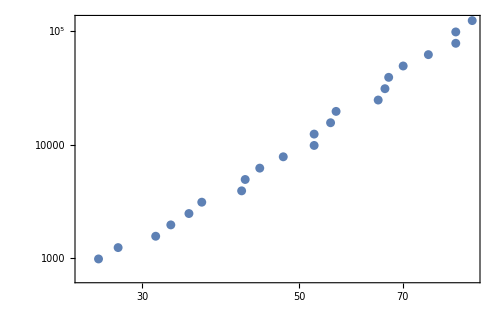

```mathematica
peakSNIIDistancevsMLNumericOptimizationPlot=ListLogLogPlot[peakSNIIDistancevsMLNumericOptimizationTab,
Frame->True,BaseStyle->{FontSize->17,FontFamily->"Latin Modern Roman"},
(*PlotRange->{{12,20},{10^-4,500}},*)
(*FrameTicks->{{logTick[-3,6,1.5,1],logTickNone[-3,6,1.5,1]},{logTick[1,3,1.5,1],Automatic}},*)
FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],FrameLabel->{{MaTeX["\\text{Matchlight}
",Magnification->1.5],None},
{MaTeX["\\text{SN IIP Distance [Mpc]}",Magnification->1.5],None}},ImageSize->500]
```

```mathematica
fitIIPeakDistances=NonlinearModelFit[Log10[peakSNIIDistancevsMLNumericOptimizationTab],a*logD+b,{a,b},logD]
```

FittedModel[…]

```mathematica
logpeakSNIIMLvsDistanceNumericOptimizationInterp[logD_]=Normal[fitIIPeakDistances]
```

-2.81739+4.03213 logD

```mathematica
(*peakSNIIDistancevsMLNumericOptimizationTab=DeleteDuplicatesBy[peakSNIIDistancevsMLNumericOptimizationTab,First]*)
```

```mathematica
(*logpeakSNIIMLvsDistanceNumericOptimizationInterp=Interpolation[Log10[peakSNIIDistancevsMLNumericOptimizationTab],InterpolationOrder->1]*)
```

```mathematica
peakSNIIMLvsDistanceNumericOptimization[distanceMpc_]:=Evaluate[Power[10,logpeakSNIIMLvsDistanceNumericOptimizationInterp[Log10[distanceMpc]]]]
```

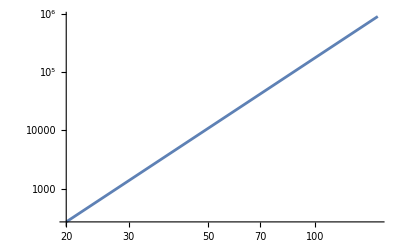

```mathematica
fitIIPeakDistancesPlot=LogLogPlot[peakSNIIMLvsDistanceNumericOptimization[distanceMpc],{distanceMpc,20,150}]
```

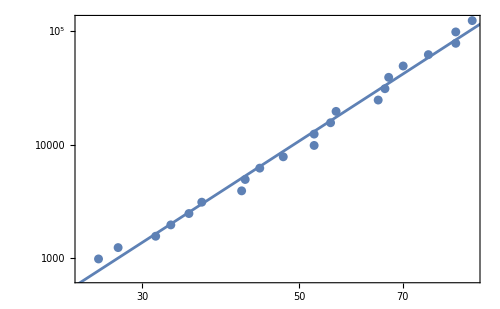

```mathematica
Show[peakSNIIDistancevsMLNumericOptimizationPlot,fitIIPeakDistancesPlot]
```

```mathematica
LocalTickmofDistanceWithCVBlueSNTypeIINumericOptimization[j_]:=Table[{Log10[peakSNIIMLvsDistanceNumericOptimization[10^(j+Log10[k])]],
tickNum=10^(j+Log10[k]);
maTexTickNum=changeStyle[Darker[color[1],.3]]@MaTeX[tickNum,Magnification->1.75]},{k,2,9}];

distanceWithCVTabBlueSNTypeIINumericOptimization=Flatten[Table[Join[{{Log10[peakSNIIMLvsDistanceNumericOptimization[10^j]],Which[(*EvenQ[j],"",*)
j==0,MaTeX[1,Magnification->1.75],
j==1,changeStyle[Darker[color[1],.3]]@MaTeX[10,Magnification->1.75],
j==2,changeStyle[Darker[color[1],.3]]@MaTeX[100,Magnification->1.75],True,changeStyle[Darker[color[1],.3]]@MaTeX[Power[10,ToString[j]],Magnification->1.75]],{0.025,0}}},
Table[
Join[LocalTickmofDistanceWithCVBlueSNTypeIINumericOptimization[j][[k]],{{0.5*.025,0}}](*Length of small ticks*),{k,1,Length[LocalTickmofDistanceWithCVBlueSNTypeIINumericOptimization[j]]}]
],{j,0,2,1}],1];//Quiet
manualTicksTabNumericOptimization=Table[{Log10[peakSNIIMLvsDistanceNumericOptimization[i]],changeStyle[Darker[color[1],.3]]@MaTeX[i,Magnification->1.75],{0.0125,0}},{i,125,150,25}]
```

{{5.63763,-Graphics-,{0.0125,0}},{5.95689,-Graphics-,{0.0125,0}}}

```mathematica
manualTicksTabNumericOptimization1=Table[{Log10[peakSNIIMLvsDistanceNumericOptimization[i]],changeStyle[Darker[color[1],.3]]@MaTeX[i,Magnification->1.55],{0.0125,0}},{i,20,100,10}]
```

{{2.42853,-Graphics-,{0.0125,0}},{3.13855,-Graphics-,{0.0125,0}},{3.64232,-Graphics-,{0.0125,0}},{4.03308,-Graphics-,{0.0125,0}},{4.35235,-Graphics-,{0.0125,0}},{4.62229,-Graphics-,{0.0125,0}},{4.85612,-Graphics-,{0.0125,0}},{5.06237,-Graphics-,{0.0125,0}},{5.24687,-Graphics-,{0.0125,0}}}

```mathematica
manualTicksTabNumericOptimization2=Table[{Log10[peakSNIIMLvsDistanceNumericOptimization[i]],changeStyle[Darker[color[1],.3]]@MaTeX[i,Magnification->1.55],{0.0125,0}},{i,150,200,50}]
```

{{5.95689,-Graphics-,{0.0125,0}},{6.46066,-Graphics-,{0.0125,0}}}

```mathematica
combinedDistanceWithCVTabBlueSNTypeIINumericOptimization=Join[(*distanceWithCVTabBlueSNTypeIINumericOptimization[[1;;19]],*)manualTicksTabNumericOptimization1,manualTicksTabNumericOptimization2]
```

{{2.42853,-Graphics-,{0.0125,0}},{3.13855,-Graphics-,{0.0125,0}},{3.64232,-Graphics-,{0.0125,0}},{4.03308,-Graphics-,{0.0125,0}},{4.35235,-Graphics-,{0.0125,0}},{4.62229,-Graphics-,{0.0125,0}},{4.85612,-Graphics-,{0.0125,0}},{5.06237,-Graphics-,{0.0125,0}},{5.24687,-Graphics-,{0.0125,0}},{5.95689,-Graphics-,{0.0125,0}},{6.46066,-Graphics-,{0.0125,0}}}

##### Matchlight Plots

```mathematica
numericalσHoverHvsMLPlotTypeII=ListPlot[{
Log10[meanNumericalTypeIIvsMatchlightTab/.{x_,y_}->{x*figureOfMeritStnd,y}],
Log10[upperNumericalTypeIIvsMatchlightTab/.{x_,y_}->{x*figureOfMeritStnd,y}],
Log10[lowerNumericalTypeIIvsMatchlightTab/.{x_,y_}->{x*figureOfMeritStnd,y}]
},
Joined->True,Filling->{2->{3}},FillingStyle->{Directive[Darker[color[3],0],Opacity[.75]]},PlotStyle->{
{AbsoluteThickness[2],Opacity[.9],color[1]},
{AbsoluteThickness[.5],Opacity[.5],color[1]},
{AbsoluteThickness[.5],Opacity[.5],color[1]}
},Frame->True,Axes->False,PlotRange->{{Log10[1*10^3],Log10[1*10^5]},{Log10[1*10^-3],Log10[2*10^-1]}},FrameTicks->{{logTick[-3,3,1.75,1],logTickNone[-3,3,1.75,1]},{logTick[2,6,1.75,1],combinedDistanceWithCVTabBlueSNTypeIINumericOptimization}},FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],FrameLabel->{{MaTeX["
\\sigma_{H_0}/H_0
",Magnification->1.75],None},{MaTeX["\\text{Interferometer Matchlight}",Magnification->1.75]
(*MaTeX["\\text{Matchlight }\\equiv [1 \\, \\rm{meter^2/picosecond^{1/2}}]",Magnification->1.5]*),None}},ImageSize->600,AspectRatio->1/3,(*1/2,*)ImagePadding->{{80,20},{70,70}},Epilog->{Inset[Style[Rotate[changeStyle[Darker[color[3],.3]]@MaTeX["\\text{Coarse-Grained Numerical Optimization}",Magnification->1.35],-10 Degree]],Scaled[{.5,0.65}]]}]
```

-Graphics-

##### Interpolation

```mathematica
logmeanNumericalTypeIIvsMatchlightInterp=Interpolation[Log10[meanNumericalTypeIIvsMatchlightTab/.{x_,y_}->{x*figureOfMeritStnd,y}],InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
meanNumericalTypeIIvsMatchlightInterp[matchlight_]:=Evaluate[Power[10,logmeanNumericalTypeIIvsMatchlightInterp[Log10[matchlight]]]]
```

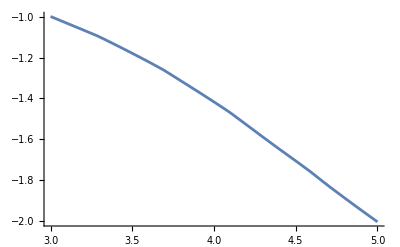

```mathematica
Plot[Log10[meanNumericalTypeIIvsMatchlightInterp[10^logmatchlight]],{logmatchlight,3,5}]
```

```mathematica
meanNumericalTypeIIvsMatchlightInterp[1250]
```

0.0932182

```mathematica
meanNumericalTypeIIvsMatchlightInterp[50000]
```

0.0148658

#### Type Ia

##### Analysis (and Optimization vs Matchlight)

```mathematica
snrEnhancementTab=Table[10^logSNREnhancement,{logSNREnhancement,-.1,2,.1}]
```

{0.794328,1.,1.25893,1.58489,1.99526,2.51189,3.16228,3.98107,5.01187,6.30957,7.94328,10.,12.5893,15.8489,19.9526,25.1189,31.6228,39.8107,50.1187,63.0957,79.4328,100.}

```mathematica
coarseTab=Table[(1/2)^i,{i,1,2}]
```

{1/2,1/4}

```mathematica
findZeroCoarsenessσHoverH[dataTab_]:=(
fit=NonlinearModelFit[dataTab,a*x+b,{a,b},x];
fitFunction=Normal[fit];
intercept=fitFunction/.{x->0}
)
```

```mathematica
findPeakTypeIaDistance[inputCoarseSNList_,timeTab_,timeSol_]:=(
timeTabSol=timeTab/.minSol[[2]];
tObsSolTab=Table[{inputCoarseSNList[[i,1]],timeTabSol[[i]]*inputCoarseSNList[[i,2]]},{i,1,Length[inputCoarseSNList]}];

peakObsTime=Max[tObsSolTab[[All,2]]];
peakObsTimePos=Last[Position[tObsSolTab[[All,2]],peakObsTime]][[1]];
peakApparentMag=tObsSolTab[[peakObsTimePos,1]];
peakDistanceIa=Dofm[peakApparentMag,MSNIa]
)
```

```mathematica
numericalMinimizationTypeIa[inputSNList_,totalObsTime_,snrEnhancement_]:=(
snPopList=inputSNList;
coarseVSσHOverHTab=Table[
coarseSNPopTab=Round[snPopList,coarseTab[[i]]];
gatherTab=Gather[coarseSNPopTab][[1;;-1]];
lengthCoarseTab=Table[{gatherTab[[i,1]],Length[gatherTab[[i]]]},{i,1,Length[gatherTab]}];
timeTab=Table[ToExpression["t"<>ToString[i]],{i,1,Length[lengthCoarseTab]}];
sumTimeTab=Sum[timeTab[[i]]*lengthCoarseTab[[i,2]],{i,1,Length[timeTab]}]==totalObsTime;
inequalityTimeTab=Table[timeTab[[i]]>10^-8,{i,1,Length[timeTab]}];
constraints=Flatten[{sumTimeTab,inequalityTimeTab}];

lagrangianNumerator=1+Sum[(lengthCoarseTab[[i,2]]*fCVSNTypeIa[lengthCoarseTab[[i,1]]]^2)/(σDoverDt[lengthCoarseTab[[i,1]],snrEnhancement,timeTab[[i]]]^2+σvSNTypeIa[lengthCoarseTab[[i,1]]]^2),{i,1,Length[lengthCoarseTab]}];

lagrangianDenominatorSum1=Sum[lengthCoarseTab[[i,2]]/(σDoverDt[lengthCoarseTab[[i,1]],snrEnhancement,timeTab[[i]]]^2+σvSNTypeIa[lengthCoarseTab[[i,1]]]^2),{i,1,Length[lengthCoarseTab]}];

lagrangianDenominatorSum2=Sum[(lengthCoarseTab[[i,2]]/(σDoverDt[lengthCoarseTab[[i,1]],snrEnhancement,timeTab[[i]]]^2+σvSNTypeIa[lengthCoarseTab[[i,1]]]^2))*(lengthCoarseTab[[j,2]]/(σDoverDt[lengthCoarseTab[[j,1]],snrEnhancement,timeTab[[j]]]^2+σvSNTypeIa[lengthCoarseTab[[j,1]]]^2))*(fCVSNTypeIa[lengthCoarseTab[[i,1]]]-fCVSNTypeIa[lengthCoarseTab[[j,1]]])^2,
{i,1,Length[lengthCoarseTab]},{j,1,Length[lengthCoarseTab]}];

lagrangian=√(lagrangianNumerator/(lagrangianDenominatorSum1+lagrangianDenominatorSum2));

minSol=NMinimize[{lagrangian,constraints},timeTab,Method->"SimulatedAnnealing"(*,AccuracyGoal->6*)(*6*),MaxIterations->1000];
minσHoverHTot=minSol[[1]];
peakTypeIaDistance=findPeakTypeIaDistance[lengthCoarseTab,timeTab,minSol[[2]]];
{coarseTab[[i]],minσHoverHTot,peakTypeIaDistance}
,{i,1,Length[coarseTab]}];

σHOverHvsCoarsenessTab=coarseVSσHOverHTab[[All,1;;2]];
peakDistancevsCoarsenessTab=coarseVSσHOverHTab[[All,3]];

{findZeroCoarsenessσHoverH[σHOverHvsCoarsenessTab],Mean[peakDistancevsCoarsenessTab]}
)

numericalMinimizationTypeIaPopulation[totalObsTime_,snrEnhancement_]:=(
Table[
startingSNPop=snPopulationTrialsTypeIa[[i]];
{numericalMinimizationTypeIa[startingSNPop,totalObsTime,snrEnhancement]},
{i,1,numTrials}]
)
```

```mathematica
numericalMinimizationTypeIaPopulation[365*6*numYrs,100]
```

{{{0.00247445,158.489}},{{0.0023445,158.489}},{{0.00233854,149.872}},{{0.0024028,158.489}},{{0.00228579,149.872}},{{0.00233725,149.872}},{{0.0023346,149.872}},{{0.00234814,149.872}},{{0.00240567,158.489}},{{0.00233971,158.489}}}

```mathematica
minSol
```

```mathematica
timeTabSol=timeTab/.minSol[[2]]
```

{5475.}

```mathematica
tObsSolTab=Table[{lengthCoarseTab[[i,1]],timeTabSol[[i]]*lengthCoarseTab[[i,2]]},{i,1,Length[lengthCoarseTab]}]
```

{{39/4,0.360911},{43/4,0.46421},{23/2,0.80106},{47/4,1.4567},{12,0.805921},{49/4,0.536749},{51/4,1.07713},{13,1.14196},{53/4,5.10082},{27/2,6.94088},{55/4,11.0682},{14,4.08838},{57/4,14.8914},{29/2,21.4513},{59/4,42.9488},{15,64.6592},{61/4,96.4157},{31/2,125.005},{63/4,67.1832},{16,9.96398},{65/4,0.565892},{33/2,133.353},{67/4,969.27},{17,2135.},{69/4,3569.42},{35/2,3665.92},{71/4,0.0000697195},{18,0.112946},{73/4,0.00001684},{37/2,0.00002217},{75/4,0.00002963},{19,0.00003957},{77/4,0.00005328},{39/2,0.00007103},{79/4,-0.000339197},{20,0.00005677}}

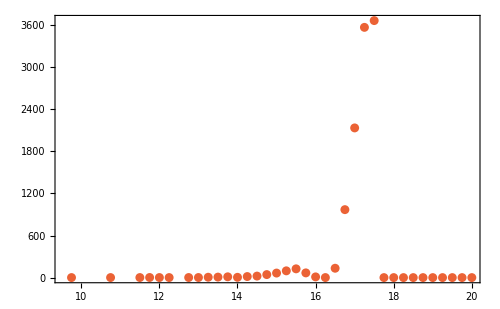

```mathematica
deltam1Over4Plot=ListPlot[tObsSolTab,PlotRange->All,Frame->True,BaseStyle->{FontSize->17,FontFamily->"Latin Modern Roman"},FrameLabel->{{MaTeX["t_{\\rm obs} \\, \\rm [hr]
",Magnification->1.5],None},
{MaTeX["m",Magnification->1.5],None}},ImageSize->500,PlotStyle->color[4]]
```

```mathematica
σHoverHNumericalTypeIavsMatchlight[tTotalObservationhr_?NumericQ]:=(
ParallelTable[
snrEnhancementIterator=snrEnhancementTab[[i]];
histogramNumericalTypeIa=numericalMinimizationTypeIaPopulation[tTotalObservationhr,snrEnhancementIterator];
numericStatPlusSysTypeIa=histogramNumericalTypeIa[[All,1,1]];
numericPeakDistanceTypeIa=histogramNumericalTypeIa[[All,1,2]];
{Mean[numericStatPlusSysTypeIa],Quantile[numericStatPlusSysTypeIa,{oneσLowerQuantile,oneσUpperQuantile}],Mean[numericPeakDistanceTypeIa]},{i,1,Length[snrEnhancementTab]}
])
```

```mathematica
(*Uncomment to run new realization*)
(*σHoverHNumericalTypeIavsMatchlightTab=σHoverHNumericalTypeIavsMatchlight[365*6*numYrs]*)
```

```mathematica
(*Export[NotebookDirectory[]<>"Data/σHoverHNumericalTypeIavsMatchlightTab.m",σHoverHNumericalTypeIavsMatchlightTab]*)
```

```mathematica
σHoverHNumericalTypeIavsMatchlightTab=Import[NotebookDirectory[]<>"Data/σHoverHNumericalTypeIavsMatchlightTab.m"]
```

{{0.041494,{0.0406883,0.042442},50.4245},{0.0365196,{0.0358291,0.0372806},51.3418},{0.0319534,{0.0313153,0.0324989},53.2137},{0.0278223,{0.0274237,0.0283345},61.7234},{0.0244248,{0.0239103,0.0248826},62.7527},{0.0213466,{0.0209877,0.0216471},63.8656},{0.0186234,{0.0182953,0.0189502},66.2222},{0.0161554,{0.0159773,0.0163456},67.856},{0.0140126,{0.0138643,0.0142247},78.1371},{0.0122729,{0.012154,0.0125415},79.9174},{0.0107549,{0.0106484,0.0109414},81.3713},{0.00934703,{0.00913358,0.00948728},84.8227},{0.0080226,{0.00787958,0.0081493},95.7092},{0.00703443,{0.00694001,0.00717954},100.61},{0.0061438,{0.00603197,0.00620829},101.22},{0.00535511,{0.00528666,0.00545056},106.101},{0.00469031,{0.00456051,0.00485011},105.491},{0.00406112,{0.003985,0.00413785},122.47},{0.00355634,{0.00350365,0.00360521},125.893},{0.00314798,{0.00306324,0.00315895},129.827},{0.00275602,{0.00266792,0.00281929},135.297},{0.00247421,{0.00232728,0.00242594},157.45}}

```mathematica
meanNumericalTypeIavsMatchlightTab=Table[{snrEnhancementTab[[i]],σHoverHNumericalTypeIavsMatchlightTab[[i,1]]},{i,1,Length[σHoverHNumericalTypeIavsMatchlightTab]}]
```

{{0.794328,0.041494},{1.,0.0365196},{1.25893,0.0319534},{1.58489,0.0278223},{1.99526,0.0244248},{2.51189,0.0213466},{3.16228,0.0186234},{3.98107,0.0161554},{5.01187,0.0140126},{6.30957,0.0122729},{7.94328,0.0107549},{10.,0.00934703},{12.5893,0.0080226},{15.8489,0.00703443},{19.9526,0.0061438},{25.1189,0.00535511},{31.6228,0.00469031},{39.8107,0.00406112},{50.1187,0.00355634},{63.0957,0.00314798},{79.4328,0.00275602},{100.,0.00247421}}

```mathematica
upperNumericalTypeIavsMatchlightTab=Table[{snrEnhancementTab[[i]],σHoverHNumericalTypeIavsMatchlightTab[[i,2,2]]},{i,1,Length[σHoverHNumericalTypeIavsMatchlightTab]}]
```

{{0.794328,0.042442},{1.,0.0372806},{1.25893,0.0324989},{1.58489,0.0283345},{1.99526,0.0248826},{2.51189,0.0216471},{3.16228,0.0189502},{3.98107,0.0163456},{5.01187,0.0142247},{6.30957,0.0125415},{7.94328,0.0109414},{10.,0.00948728},{12.5893,0.0081493},{15.8489,0.00717954},{19.9526,0.00620829},{25.1189,0.00545056},{31.6228,0.00485011},{39.8107,0.00413785},{50.1187,0.00360521},{63.0957,0.00315895},{79.4328,0.00281929},{100.,0.00242594}}

```mathematica
lowerNumericalTypeIavsMatchlightTab=Table[{snrEnhancementTab[[i]],σHoverHNumericalTypeIavsMatchlightTab[[i,2,1]]},{i,1,Length[σHoverHNumericalTypeIavsMatchlightTab]}]
```

{{0.794328,0.0406883},{1.,0.0358291},{1.25893,0.0313153},{1.58489,0.0274237},{1.99526,0.0239103},{2.51189,0.0209877},{3.16228,0.0182953},{3.98107,0.0159773},{5.01187,0.0138643},{6.30957,0.012154},{7.94328,0.0106484},{10.,0.00913358},{12.5893,0.00787958},{15.8489,0.00694001},{19.9526,0.00603197},{25.1189,0.00528666},{31.6228,0.00456051},{39.8107,0.003985},{50.1187,0.00350365},{63.0957,0.00306324},{79.4328,0.00266792},{100.,0.00232728}}

##### Peak Distances

```mathematica
σHoverHNumericalTypeIavsMatchlightTab[[1,1]]
```

0.041494

```mathematica
peakSNIaDistancevsMLNumericOptimizationTab=Table[{snrEnhancementTab[[i]]*matchLightStnd,σHoverHNumericalTypeIavsMatchlightTab[[i,3]]},{i,1,Length[σHoverHNumericalTypeIavsMatchlightTab]}]
```

{{986.415,50.4245},{1241.82,51.3418},{1563.36,53.2137},{1968.16,61.7234},{2477.76,62.7527},{3119.32,63.8656},{3926.99,66.2222},{4943.79,67.856},{6223.86,78.1371},{7835.38,79.9174},{9864.15,81.3713},{12418.2,84.8227},{15633.6,95.7092},{19681.6,100.61},{24777.6,101.22},{31193.2,106.101},{39269.9,105.491},{49437.9,122.47},{62238.6,125.893},{78353.8,129.827},{98641.5,135.297},{124182.,157.45}}

```mathematica
peakSNIaDistancevsMLNumericOptimizationTab=peakSNIaDistancevsMLNumericOptimizationTab/.{x_,y_}->{y,x}
```

{{50.4245,986.415},{51.3418,1241.82},{53.2137,1563.36},{61.7234,1968.16},{62.7527,2477.76},{63.8656,3119.32},{66.2222,3926.99},{67.856,4943.79},{78.1371,6223.86},{79.9174,7835.38},{81.3713,9864.15},{84.8227,12418.2},{95.7092,15633.6},{100.61,19681.6},{101.22,24777.6},{106.101,31193.2},{105.491,39269.9},{122.47,49437.9},{125.893,62238.6},{129.827,78353.8},{135.297,98641.5},{157.45,124182.}}

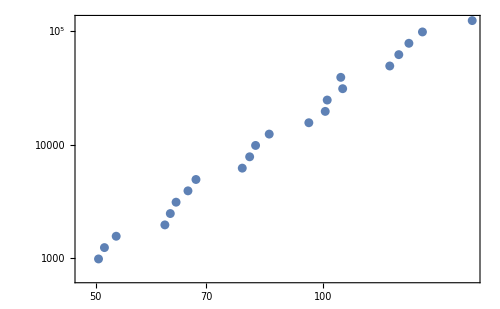

```mathematica
peakSNIaDistancevsMLNumericOptimizationPlot=ListLogLogPlot[peakSNIaDistancevsMLNumericOptimizationTab,Frame->True,BaseStyle->{FontSize->17,FontFamily->"Latin Modern Roman"},
(*PlotRange->{{12,20},{10^-4,500}},*)
(*FrameTicks->{{logTick[-3,6,1.5,1],logTickNone[-3,6,1.5,1]},{logTick[1,3,1.5,1],Automatic}},*)
FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],FrameLabel->{{MaTeX["\\text{Matchlight}
",Magnification->1.5],None},
{MaTeX["\\text{SN Ia Distance [Mpc]}",Magnification->1.5],None}},ImageSize->500]
```

```mathematica
fitIaPeakDistances=NonlinearModelFit[Log10[peakSNIaDistancevsMLNumericOptimizationTab],a*logD+b,{a,b},logD]
```

FittedModel[…]

```mathematica
logpeakSNIaMLvsDistanceNumericOptimizationInterp[logD_]=Normal[fitIaPeakDistances]
```

-4.48383+4.41577 logD

```mathematica
peakSNIaDistancevsMLNumericOptimizationTab=DeleteDuplicatesBy[peakSNIaDistancevsMLNumericOptimizationTab,First]
```

{{50.4245,986.415},{51.3418,1241.82},{53.2137,1563.36},{61.7234,1968.16},{62.7527,2477.76},{63.8656,3119.32},{66.2222,3926.99},{67.856,4943.79},{78.1371,6223.86},{79.9174,7835.38},{81.3713,9864.15},{84.8227,12418.2},{95.7092,15633.6},{100.61,19681.6},{101.22,24777.6},{106.101,31193.2},{105.491,39269.9},{122.47,49437.9},{125.893,62238.6},{129.827,78353.8},{135.297,98641.5},{157.45,124182.}}

```mathematica
(*logpeakSNIaMLvsDistanceNumericOptimizationInterp=Interpolation[Log10[peakSNIaDistancevsMLNumericOptimizationTab],InterpolationOrder->1]*)
```

```mathematica
peakSNIaMLvsDistanceNumericOptimization[distanceMpc_]:=Evaluate[Power[10,logpeakSNIaMLvsDistanceNumericOptimizationInterp[Log10[distanceMpc]]]]
```

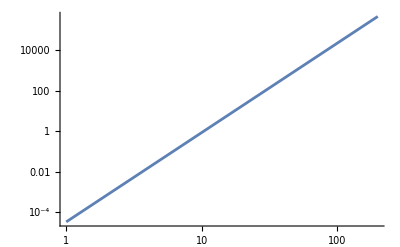

```mathematica
fitIaPeakDistancesPlot=LogLogPlot[peakSNIaMLvsDistanceNumericOptimization[dMpc],{dMpc,1,200}]
```

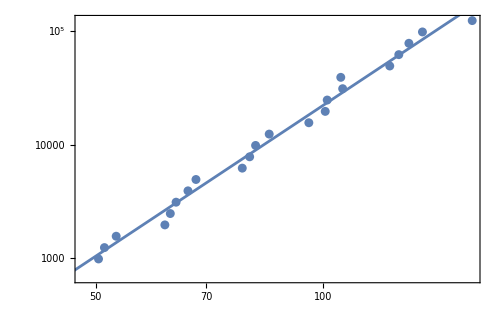

```mathematica
Show[peakSNIaDistancevsMLNumericOptimizationPlot,fitIaPeakDistancesPlot]
```

```mathematica
LocalTickmofDistanceWithCVOrangeSNTypeIaNumericOptimization[j_]:=Table[{Log10[peakSNIaMLvsDistanceNumericOptimization[10^(j+Log10[k])]],
tickNum=10^(j+Log10[k]);
maTexTickNum=changeStyle[Darker[color[2],.3]]@MaTeX[tickNum,Magnification->1.75]},{k,2,9}];

distanceWithCVTabOrangeSNTypeIaNumericOptimization=Flatten[Table[Join[{{Log10[peakSNIaMLvsDistanceNumericOptimization[10^j]],Which[(*EvenQ[j],"",*)
j==0,MaTeX[1,Magnification->1.75],
j==1,changeStyle[Darker[color[2],.3]]@MaTeX[10,Magnification->1.75],
j==2,changeStyle[Darker[color[2],.3]]@MaTeX[100,Magnification->1.75],True,changeStyle[Darker[color[2],.3]]@MaTeX[Power[10,ToString[j]],Magnification->1.75]],{0.025,0}}},
Table[
Join[LocalTickmofDistanceWithCVOrangeSNTypeIaNumericOptimization[j][[k]],{{0.5*.025,0}}](*Length of small ticks*),{k,1,Length[LocalTickmofDistanceWithCVOrangeSNTypeIaNumericOptimization[j]]}]
],{j,0,2,1}],1];//Quiet
manualTicksTabNumericOptimization=Table[{Log10[peakSNIaMLvsDistanceNumericOptimization[i]],changeStyle[Darker[color[2],.3]]@MaTeX[i,Magnification->1.75],{0.0125,0}},{i,125,150,25}]
```

{{4.77564,-Graphics-,{0.0125,0}},{5.12529,-Graphics-,{0.0125,0}}}

```mathematica
manualTicksTabNumericOptimization1=Table[{Log10[peakSNIaMLvsDistanceNumericOptimization[i]],changeStyle[Darker[color[2],.3]]@MaTeX[i,Magnification->1.55],{0.0125,0}},{i,20,100,10}]
```

{{1.26122,-Graphics-,{0.0125,0}},{2.0388,-Graphics-,{0.0125,0}},{2.5905,-Graphics-,{0.0125,0}},{3.01843,-Graphics-,{0.0125,0}},{3.36808,-Graphics-,{0.0125,0}},{3.6637,-Graphics-,{0.0125,0}},{3.91978,-Graphics-,{0.0125,0}},{4.14565,-Graphics-,{0.0125,0}},{4.34771,-Graphics-,{0.0125,0}}}

```mathematica
manualTicksTabNumericOptimization2=Table[{Log10[peakSNIaMLvsDistanceNumericOptimization[i]],changeStyle[Darker[color[2],.3]]@MaTeX[i,Magnification->1.55],{0.0125,0}},{i,125,200,25}]
```

{{4.77564,-Graphics-,{0.0125,0}},{5.12529,-Graphics-,{0.0125,0}},{5.42091,-Graphics-,{0.0125,0}},{5.67699,-Graphics-,{0.0125,0}}}

```mathematica
combinedDistanceWithCVTabOrangeSNTypeIaNumericOptimization=Join[(*distanceWithCVTabBlueSNTypeIaNumericOptimization[[1;;19]],*)manualTicksTabNumericOptimization1,manualTicksTabNumericOptimization2]
```

{{1.26122,-Graphics-,{0.0125,0}},{2.0388,-Graphics-,{0.0125,0}},{2.5905,-Graphics-,{0.0125,0}},{3.01843,-Graphics-,{0.0125,0}},{3.36808,-Graphics-,{0.0125,0}},{3.6637,-Graphics-,{0.0125,0}},{3.91978,-Graphics-,{0.0125,0}},{4.14565,-Graphics-,{0.0125,0}},{4.34771,-Graphics-,{0.0125,0}},{4.77564,-Graphics-,{0.0125,0}},{5.12529,-Graphics-,{0.0125,0}},{5.42091,-Graphics-,{0.0125,0}},{5.67699,-Graphics-,{0.0125,0}}}

##### Matchlight

```mathematica
numericalσHoverHvsMLPlotTypeIa=ListPlot[{
Log10[meanNumericalTypeIavsMatchlightTab/.{x_,y_}->{x*figureOfMeritStnd,y}](*,
Log10[upperNumericalTypeIavsMatchlightTab/.{x_,y_}->{x*figureOfMeritStnd,y}],
Log10[lowerNumericalTypeIavsMatchlightTab/.{x_,y_}->{x*figureOfMeritStnd,y}]*)
},
Joined->True,Filling->{2->{3}},FillingStyle->{Directive[Darker[color[2],0],Opacity[.75]]},PlotStyle->{
{AbsoluteThickness[2],Opacity[.9],color[2]},
{AbsoluteThickness[.5],Opacity[.5],color[2]},
{AbsoluteThickness[.5],Opacity[.5],color[2]}
},Frame->True,Axes->False,PlotRange->{{Log10[1*10^3],Log10[1*10^5]},{Log10[1*10^-3],Log10[2*10^-1]}},FrameTicks->{{logTick[-3,3,1.75,1],logTickNone[-3,3,1.75,1]},{logTick[2,6,1.75,1],combinedDistanceWithCVTabOrangeSNTypeIaNumericOptimization}},FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],FrameLabel->{{MaTeX["
\\sigma_{H_0}/H_0
",Magnification->1.75],None},{MaTeX["\\text{Interferometer Matchlight}",Magnification->1.75]
(*MaTeX["\\text{Matchlight }\\equiv [1 \\, \\rm{meter^2/picosecond^{1/2}}]",Magnification->1.5]*),None}},ImageSize->600,AspectRatio->1/3,(*1/2,*)ImagePadding->{{80,20},{70,70}},Epilog->{Inset[Style[Rotate[changeStyle[Darker[color[3],.3]]@MaTeX["\\text{Coarse-Grained Numerical Optimization}",Magnification->1.35],-10 Degree]],Scaled[{.5,0.65}]]}]
```

-Graphics-

##### Interpolation

```mathematica
logmeanNumericalTypeIavsMatchlightInterp=Interpolation[Log10[meanNumericalTypeIavsMatchlightTab/.{x_,y_}->{x*figureOfMeritStnd,y}],InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
meanNumericalTypeIavsMatchlightInterp[matchlight_]:=Evaluate[Power[10,logmeanNumericalTypeIavsMatchlightInterp[Log10[matchlight]]]]
```

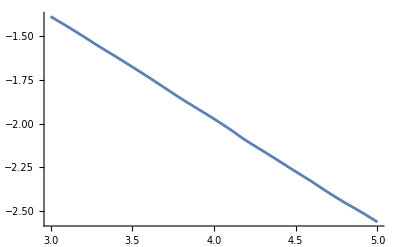

```mathematica
Plot[Log10[meanNumericalTypeIavsMatchlightInterp[10^logmatchlight]],{logmatchlight,3,5}]
```

```mathematica
meanNumericalTypeIavsMatchlightInterp[1250]
```

0.0363808

```mathematica
meanNumericalTypeIavsMatchlightInterp[50000]
```

0.00403474

#### Combined Matchlight Plot

##### SH0Es Plot

```mathematica
σPlanckSH0ESDiscrepancy=7*10^-2;
```

```mathematica
SH0ESUncertaintyPlot=Plot[{
Log10[σPlanckSH0ESDiscrepancy],
},{x,1,10},
PlotStyle->{
{AbsoluteThickness[2],Opacity[.85],color[4],Dashed},
},
Frame->True,Axes->False,PlotRange->{{Log10[500],Log10[3*10^5]},{-3,Log10[2*10^-1]}},FrameTicks->{{logTick[-3,3,1.5,1],logTickNone[-3,3,1.5,1]},{logTick[2,6,1.5,1],None}},FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],FrameLabel->{{MaTeX["
\\text{Error Budget }H_0
",Magnification->1.5],None},
{MaTeX["\\text{Interferometer Matchlight}",Magnification->1.5],None(*MaTeX["\\text{Max SN Type-II Observational Distance [Mpc]}",Magnification->1.5]*)}},ImageSize->425*.805,AspectRatio->1/(.75*GoldenRatio),
ImagePadding->{{80,20},{70,70}},
Epilog->{
Inset[Style[Rotate[changeStyle[Darker[color[2],.3]]@MaTeX["\\text{SH0ES}",Magnification->1.35],0Degree]],Scaled[{.2,0.38}]]
}]
```

-Graphics-

##### Combined σH/H Plot No Two Axes Ticks

```mathematica
combinedDirectH0NumericOptimizationPlot=Show[
numericalσHoverHvsMLPlotTypeII,
numericalσHoverHvsMLPlotTypeIa,SH0ESUncertaintyPlot,
Epilog->{
Inset[Style[Rotate[changeStyle[Darker[color[1],.3]]@MaTeX["\\text{Type IIP}",Magnification->1.35],-10 Degree]],Scaled[{.75,.625}]],Inset[Style[Rotate[changeStyle[Darker[color[2],.3]]@MaTeX["\\text{Type Ia}",Magnification->1.35],-10 Degree]],Scaled[{.75,.375}]],
Inset[Framed[Style[Rotate[changeStyle[Darker[color[4],.3]]@MaTeX["({H_0}_{\\,\\rm CMB} - {H_0}_{\\, \\rm SH0ES})/{H_0}_{\\, \\rm SH0ES}",Magnification->1.35],0Degree]],Background->Directive[White,Opacity[.75]],FrameStyle->None,FrameMargins->{{None,None},{-3,-3}}],Scaled[{.75,.875}]]
}
]
```

-Graphics-

```mathematica
(*Export[NotebookDirectory[]<>"combinedDirectH0Plot.pdf",combinedDirectH0Plot]*)
```

##### Combined σH/H Plot With Two Axes Ticks

```mathematica
combinedDirectH0NumericOptimizationPlotNoTop=Show[
numericalσHoverHvsMLPlotTypeII,numericalσHoverHvsMLPlotTypeIa,SH0ESUncertaintyPlot,Frame->{True,True,False,True},ImagePadding->{{80,20},{70,30}},
Epilog->{
Inset[Style[Rotate[changeStyle[Darker[color[1],.3]]@MaTeX["\\text{Type IIP}",Magnification->1.35],-10 Degree]],Scaled[{.75,.625-.01}]],Inset[Style[Rotate[changeStyle[Darker[color[2],.3]]@MaTeX["\\text{Type Ia}",Magnification->1.35],-10 Degree]],Scaled[{.75,.375-.005}]],
Inset[Framed[Style[Rotate[changeStyle[Darker[color[4],.3]]@MaTeX["({H_0}_{\\,\\rm CMB} - {H_0}_{\\, \\rm SH0ES})/{H_0}_{\\, \\rm SH0ES}",Magnification->1.35],0Degree]],Background->Directive[White,Opacity[.75]],FrameStyle->None,FrameMargins->{{None,None},{-3,-3}}],Scaled[{.75,.86}]]
}
]
```

-Graphics-

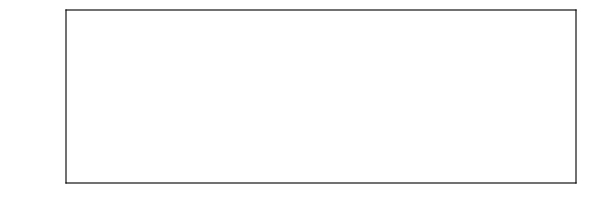

```mathematica
blueFrameTick=ListPlot[{
Log10[meanNumericalTypeIIvsMatchlightTab/.{x_,y_}->{x*figureOfMeritStnd,y}],
Log10[upperNumericalTypeIIvsMatchlightTab/.{x_,y_}->{x*figureOfMeritStnd,y}],
Log10[lowerNumericalTypeIIvsMatchlightTab/.{x_,y_}->{x*figureOfMeritStnd,y}]
},
Joined->True,Mesh->All,
Filling->{2->{3}},
FillingStyle->{Directive[Darker[color[1],0],Opacity[.75]]},
PlotStyle->None,
Frame->{False,False,True,False},Axes->False,PlotRange->{{Log10[1*10^3],Log10[1*10^5]},{Log10[5*10^-1],Log10[2*10^-1]}},FrameTicks->{{logTick[-3,3,1.5,1],logTickNone[-3,3,1.5,1]},{logTick[2,6,1.5,1],combinedDistanceWithCVTabBlueSNTypeIINumericOptimization}},FrameStyle->Directive[{color[1],AbsoluteThickness[1.75]}],FrameTicksStyle->Directive[{color[1],AbsoluteThickness[2]}],FrameLabel->{{MaTeX["
\\sigma_{H_0}/H_0
",Magnification->1.5],None},
{MaTeX["\\text{Interferometer Matchlight}",Magnification->1.5]
(*MaTeX["\\text{Matchlight }\\equiv [1 \\, \\rm{meter^2/picosecond^{1/2}}]",Magnification->1.5]*),
None}},ImageSize->600,AspectRatio->1/3,(*1/2,*)
ImagePadding->{{80,20},{70,30}}]
```

```mathematica
combinedDirectH0PlotNumericBlueTop=Overlay[{combinedDirectH0NumericOptimizationPlotNoTop,blueFrameTick}]
```

-Graphics--Graphics-

```mathematica
orangeFrameTick=ListPlot[{
Log10[meanNumericalTypeIavsMatchlightTab/.{x_,y_}->{x*figureOfMeritStnd,y}](*,
Log10[upperNumericalTypeIavsMatchlightTab/.{x_,y_}->{x*figureOfMeritStnd,y}],
Log10[lowerNumericalTypeIavsMatchlightTab/.{x_,y_}->{x*figureOfMeritStnd,y}]*)
},
Joined->True,(*Mesh->All,*)
Filling->{2->{3}},
FillingStyle->{Directive[Darker[color[2],.1],Opacity[.8]]},
PlotStyle->
None,
Frame->{False,False,True,False},Axes->False,PlotRange->{{Log10[10^3],Log10[1*10^5]},{Log10[5*10^-1],Log10[2*10^-1]}},FrameTicks->{{logTick[-3,3,1.5,1],logTickNone[-3,3,1.5,1]},{logTick[2,6,1.5,1],combinedDistanceWithCVTabOrangeSNTypeIaNumericOptimization}},FrameStyle->Directive[{color[2],AbsoluteThickness[1.75]}],FrameTicksStyle->Directive[{color[2],AbsoluteThickness[2]}],FrameLabel->{{MaTeX["
\\sigma_{H_0}/H_0
",Magnification->1.5],None},
{MaTeX["\\text{Interferometer Matchlight}",Magnification->1.5],
MaTeX["\\text{Peak SN Observational Distance [Mpc]}",Magnification->1.75]}},ImageSize->600,AspectRatio->1/100,
ImagePadding->{{80,20},{10,70}}]
```

-Graphics-

```mathematica
combinedDirectH0PlotNumericBlueandOrageTop=Grid[{{orangeFrameTick},{combinedDirectH0PlotNumericBlueTop}},Spacings->{0,-.35}]
```

-Graphics-
-Graphics--Graphics-

```mathematica
Export[NotebookDirectory[]<>"Figures/combinedDirectH0NumericOptimizationPlot.pdf",combinedDirectH0PlotNumericBlueandOrageTop]
```

/Users/david/Documents/Projects/EPIC Hubble/Github Code/Figures/combinedDirectH0NumericOptimizationPlot.pdf